## 733448815501 - Concatinated successfully

### Observations: Roll further to make it more complete

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

```mathematica
rs01=FromReducedRankIndex[733448815501]
```

<|Index→733448815501,QCode→32342434232432334,RuleSet→{AA→AB,BB→AA,BA→AAB}|>

```mathematica
rs01[["RuleSet"]]
```

{AA→AB,BB→AA,BA→AAB}


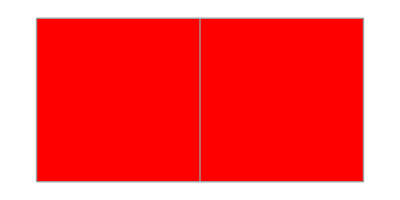


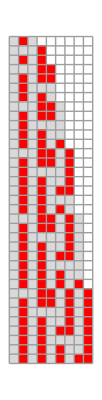
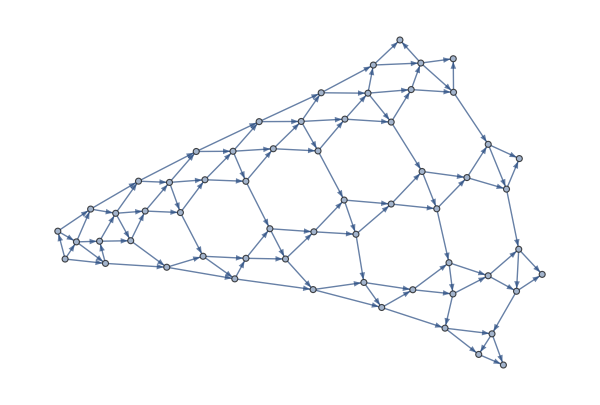
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss01=SSS[rs01[["RuleSet"]], "ABA",4000,
 SSSMax->35,NetMax->60,NetSize->{600,Automatic},SSSSize->{Automatic,380},HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->304.,NetSize->{Automatic,338.},SSSSize->{Automatic,486.},IconSize->{Automatic,31.8},VertexSize->Automatic];
```

```mathematica
sss01[["Net"]]//Short
```

{1→2,2→3,1→3,2→4,3→4,3→5,1→5,3→6,5→6,4→7,6→7,4→8,7→8,7→9,6→9,«7967»,3992→3993,3992→3994,3887→3994,3994→3995,3887→3995,3994→3996,3995→3996,3889→3997,3891→3997,3889→3998,3997→3998,3997→3999,3891→3999,3997→4000,3999→4000}

```mathematica
nds01=ToNetDifferenceSets[sss01[["Net"]]]
```

{{1,2,4},{1,2},{1,2,3},{3,4},{1,6},{1,3},{1,2,3},{4,5},{1,2},{2,4},{5,6},{1,2,3},{6,7},{1,2},{4,6},{1,2},{1,9},{5,6},{1,2,3},{7,8},{1,2},{5,7},{1,2},{1,2},{6,7},{8,9},{1,2,3},{9,10},{1,2},{7,9},{1,2},{1,2},{8,9},{1,2},{1,12},{8,9},{1,2,3},{10,11},{1,2},{8,10},{1,2},{1,2},{9,10},{1,2},{1,2},{9,10},{11,12},{1,2,3},{12,13},{1,2},{10,12},{1,2},{1,2},{11,12},{1,2},{1,2},{11,12},{1,2},{1,15},{11,12},{1,2,3},{13,14},{1,2},{11,13},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{14,15},{1,2,3},{15,16},{1,2},{13,15},{1,2},{1,2},{14,15},{1,2},{1,2},{14,15},{1,2},{1,2},{14,15},{1,2},{1,18},{14,15},{1,2,3},{16,17},{1,2},{14,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{17,18},{1,2,3},{18,19},{1,2},{16,18},{1,2},{1,2},{17,18},{1,2},{1,2},{17,18},{1,2},{1,2},{17,18},{1,2},{1,2},{17,18},{1,2},{1,21},{17,18},{1,2,3},{19,20},{1,2},{17,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{20,21},{1,2,3},{21,22},{1,2},{19,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,24},{20,21},{1,2,3},{22,23},{1,2},{20,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{23,24},{1,2,3},{24,25},{1,2},{22,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,27},{23,24},{1,2,3},{25,26},{1,2},{23,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{26,27},{1,2,3},{27,28},{1,2},{25,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,30},{26,27},{1,2,3},{28,29},{1,2},{26,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{29,30},{1,2,3},{30,31},{1,2},{28,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,33},{29,30},{1,2,3},{31,32},{1,2},{29,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{32,33},{1,2,3},{33,34},{1,2},{31,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,36},{32,33},{1,2,3},{34,35},{1,2},{32,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{35,36},{1,2,3},{36,37},{1,2},{34,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,39},{35,36},{1,2,3},{37,38},{1,2},{35,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{38,39},{1,2,3},{39,40},{1,2},{37,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,42},{38,39},{1,2,3},{40,41},{1,2},{38,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{41,42},{1,2,3},{42,43},{1,2},{40,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,45},{41,42},{1,2,3},{43,44},{1,2},{41,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{44,45},{1,2,3},{45,46},{1,2},{43,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,48},{44,45},{1,2,3},{46,47},{1,2},{44,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{47,48},{1,2,3},{48,49},{1,2},{46,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,51},{47,48},{1,2,3},{49,50},{1,2},{47,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{50,51},{1,2,3},{51,52},{1,2},{49,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,54},{50,51},{1,2,3},{52,53},{1,2},{50,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{53,54},{1,2,3},{54,55},{1,2},{52,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,57},{53,54},{1,2,3},{55,56},{1,2},{53,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{56,57},{1,2,3},{57,58},{1,2},{55,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,60},{56,57},{1,2,3},{58,59},{1,2},{56,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{59,60},{1,2,3},{60,61},{1,2},{58,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,63},{59,60},{1,2,3},{61,62},{1,2},{59,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{62,63},{1,2,3},{63,64},{1,2},{61,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,66},{62,63},{1,2,3},{64,65},{1,2},{62,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{65,66},{1,2,3},{66,67},{1,2},{64,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,69},{65,66},{1,2,3},{67,68},{1,2},{65,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{68,69},{1,2,3},{69,70},{1,2},{67,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,72},{68,69},{1,2,3},{70,71},{1,2},{68,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{71,72},{1,2,3},{72,73},{1,2},{70,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,75},{71,72},{1,2,3},{73,74},{1,2},{71,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{74,75},{1,2,3},{75,76},{1,2},{73,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,78},{74,75},{1,2,3},{76,77},{1,2},{74,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{77,78},{1,2,3},{78,79},{1,2},{76,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,81},{77,78},{1,2,3},{79,80},{1,2},{77,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{80,81},{1,2,3},{81,82},{1,2},{79,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,84},{80,81},{1,2,3},{82,83},{1,2},{80,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{83,84},{1,2,3},{84,85},{1,2},{82,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,87},{83,84},{1,2,3},{85,86},{1,2},{83,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{86,87},{1,2,3},{87,88},{1,2},{85,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,90},{86,87},{1,2,3},{88,89},{1,2},{86,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{89,90},{1,2,3},{90,91},{1,2},{88,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,93},{89,90},{1,2,3},{91,92},{1,2},{89,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{92,93},{1,2,3},{93,94},{1,2},{91,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,96},{92,93},{1,2,3},{94,95},{1,2},{92,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{95,96},{1,2,3},{96,97},{1,2},{94,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,99},{95,96},{1,2,3},{97,98},{1,2},{95,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{98,99},{1,2,3},{99,100},{1,2},{97,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,102},{98,99},{1,2,3},{100,101},{1,2},{98,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{101,102},{1,2,3},{102,103},{1,2},{100,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,105},{101,102},{1,2,3},{103,104},{1,2},{101,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{104,105},{1,2,3},{105,106},{1,2},{103,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,108},{104,105},{1,2,3},{106,107},{1,2},{104,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{107,108},{1,2,3},{108,109},{1,2},{106,108},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1},{},{1,2,3},{},{1}}

```mathematica
Position[nds01,{105,106}]
```

{{3676},{3787},{3790},{3793},{3796},{3799},{3802},{3805},{3808},{3811},{3814},{3817},{3820},{3823},{3826},{3829},{3832},{3835},{3838},{3841},{3844},{3847},{3850},{3853},{3856},{3859},{3862},{3865},{3868},{3871},{3874},{3877},{3880},{3883},{3886}}

```mathematica
$debug=True;
```

```mathematica
rsl01=ReduceSetList[nds01[[1;;3886]]]
```

Entering ReduceSetList with: {{1,2,4},{1,2},{1,2,3},{3,4},{1,6},{1,3},{1,2,3},{4,5},{1,2},{2,4},{5,6},{1,2,3},{6,7},{1,2},{4,6},{1,2},{1,9},{5,6},{1,2,3},{7,8},{1,2},{5,7},{1,2},{1,2},{6,7},{8,9},{1,2,3},{9,10},{1,2},{7,9},{1,2},{1,2},{8,9},{1,2},{1,12},{8,9},{1,2,3},{10,11},{1,2},{8,10},{1,2},{1,2},{9,10},{1,2},{1,2},{9,10},{11,12},{1,2,3},{12,13},{1,2},{10,12},{1,2},{1,2},{11,12},{1,2},{1,2},{11,12},{1,2},{1,15},{11,12},{1,2,3},{13,14},{1,2},{11,13},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{14,15},{1,2,3},{15,16},{1,2},{13,15},{1,2},{1,2},{14,15},{1,2},{1,2},{14,15},{1,2},{1,2},{14,15},{1,2},{1,18},{14,15},{1,2,3},{16,17},{1,2},{14,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{17,18},{1,2,3},{18,19},{1,2},{16,18},{1,2},{1,2},{17,18},{1,2},{1,2},{17,18},{1,2},{1,2},{17,18},{1,2},{1,2},{17,18},{1,2},{1,21},{17,18},{1,2,3},{19,20},{1,2},{17,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{20,21},{1,2,3},{21,22},{1,2},{19,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,24},{20,21},{1,2,3},{22,23},{1,2},{20,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{23,24},{1,2,3},{24,25},{1,2},{22,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,27},{23,24},{1,2,3},{25,26},{1,2},{23,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{26,27},{1,2,3},{27,28},{1,2},{25,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,30},{26,27},{1,2,3},{28,29},{1,2},{26,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{29,30},{1,2,3},{30,31},{1,2},{28,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,33},{29,30},{1,2,3},{31,32},{1,2},{29,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{32,33},{1,2,3},{33,34},{1,2},{31,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,36},{32,33},{1,2,3},{34,35},{1,2},{32,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{35,36},{1,2,3},{36,37},{1,2},{34,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,39},{35,36},{1,2,3},{37,38},{1,2},{35,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{38,39},{1,2,3},{39,40},{1,2},{37,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,42},{38,39},{1,2,3},{40,41},{1,2},{38,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{41,42},{1,2,3},{42,43},{1,2},{40,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,45},{41,42},{1,2,3},{43,44},{1,2},{41,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{44,45},{1,2,3},{45,46},{1,2},{43,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,48},{44,45},{1,2,3},{46,47},{1,2},{44,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{47,48},{1,2,3},{48,49},{1,2},{46,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,51},{47,48},{1,2,3},{49,50},{1,2},{47,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{50,51},{1,2,3},{51,52},{1,2},{49,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,54},{50,51},{1,2,3},{52,53},{1,2},{50,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{53,54},{1,2,3},{54,55},{1,2},{52,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,57},{53,54},{1,2,3},{55,56},{1,2},{53,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{56,57},{1,2,3},{57,58},{1,2},{55,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,60},{56,57},{1,2,3},{58,59},{1,2},{56,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{59,60},{1,2,3},{60,61},{1,2},{58,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,63},{59,60},{1,2,3},{61,62},{1,2},{59,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{62,63},{1,2,3},{63,64},{1,2},{61,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,66},{62,63},{1,2,3},{64,65},{1,2},{62,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{65,66},{1,2,3},{66,67},{1,2},{64,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,69},{65,66},{1,2,3},{67,68},{1,2},{65,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{68,69},{1,2,3},{69,70},{1,2},{67,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,72},{68,69},{1,2,3},{70,71},{1,2},{68,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{71,72},{1,2,3},{72,73},{1,2},{70,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,75},{71,72},{1,2,3},{73,74},{1,2},{71,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{74,75},{1,2,3},{75,76},{1,2},{73,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,78},{74,75},{1,2,3},{76,77},{1,2},{74,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{1,2},{1,2},{75,76},{77,78},{1,2,3},{78,79},{1,2},{76,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,2},{77,78},{1,2},{1,81},{77,78},{1,2,3},{79,80},{1,2},{77,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{1,2},{1,2},{78,79},{80,81},{1,2,3},{81,82},{1,2},{79,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,2},{80,81},{1,2},{1,84},{80,81},{1,2,3},{82,83},{1,2},{80,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{1,2},{1,2},{81,82},{83,84},{1,2,3},{84,85},{1,2},{82,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,2},{83,84},{1,2},{1,87},{83,84},{1,2,3},{85,86},{1,2},{83,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{1,2},{1,2},{84,85},{86,87},{1,2,3},{87,88},{1,2},{85,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,2},{86,87},{1,2},{1,90},{86,87},{1,2,3},{88,89},{1,2},{86,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{1,2},{1,2},{87,88},{89,90},{1,2,3},{90,91},{1,2},{88,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,2},{89,90},{1,2},{1,93},{89,90},{1,2,3},{91,92},{1,2},{89,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{1,2},{1,2},{90,91},{92,93},{1,2,3},{93,94},{1,2},{91,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,2},{92,93},{1,2},{1,96},{92,93},{1,2,3},{94,95},{1,2},{92,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{1,2},{1,2},{93,94},{95,96},{1,2,3},{96,97},{1,2},{94,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,2},{95,96},{1,2},{1,99},{95,96},{1,2,3},{97,98},{1,2},{95,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{1,2},{1,2},{96,97},{98,99},{1,2,3},{99,100},{1,2},{97,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,2},{98,99},{1,2},{1,102},{98,99},{1,2,3},{100,101},{1,2},{98,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{1,2},{1,2},{99,100},{101,102},{1,2,3},{102,103},{1,2},{100,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,2},{101,102},{1,2},{1,105},{101,102},{1,2,3},{103,104},{1,2},{101,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{1,2},{1,2},{102,103},{104,105},{1,2,3},{105,106},{1,2},{103,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,2},{104,105},{1,2},{1,108},{104,105},{1,2,3},{106,107},{1,2},{104,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106},{1,2},{1,2},{105,106}}

exact repLen = 1: {{1,2,4},{1,2},{1,2,3},{3,4},{1,6},{1,3},{1,2,3},{4,5},{1,2},{2,4},{5,6},{1,2,3},{6,7},{1,2},{4,6},{1,2},{1,9},{5,6},{1,2,3},{7,8},{1,2},{5,7},€^2[{1,2}],{6,7},{8,9},{1,2,3},{9,10},{1,2},{7,9},€^2[{1,2}],{8,9},{1,2},{1,12},{8,9},{1,2,3},{10,11},{1,2},{8,10},€^2[{1,2}],{9,10},€^2[{1,2}],{9,10},{11,12},{1,2,3},{12,13},{1,2},{10,12},€^2[{1,2}],{11,12},€^2[{1,2}],{11,12},{1,2},{1,15},{11,12},{1,2,3},{13,14},{1,2},{11,13},€^2[{1,2}],{12,13},€^2[{1,2}],{12,13},€^2[{1,2}],{12,13},{14,15},{1,2,3},{15,16},{1,2},{13,15},€^2[{1,2}],{14,15},€^2[{1,2}],{14,15},€^2[{1,2}],{14,15},{1,2},{1,18},{14,15},{1,2,3},{16,17},{1,2},{14,16},€^2[{1,2}],{15,16},€^2[{1,2}],{15,16},€^2[{1,2}],{15,16},€^2[{1,2}],{15,16},{17,18},{1,2,3},{18,19},{1,2},{16,18},€^2[{1,2}],{17,18},€^2[{1,2}],{17,18},€^2[{1,2}],{17,18},€^2[{1,2}],{17,18},{1,2},{1,21},{17,18},{1,2,3},{19,20},{1,2},{17,19},€^2[{1,2}],{18,19},€^2[{1,2}],{18,19},€^2[{1,2}],{18,19},€^2[{1,2}],{18,19},€^2[{1,2}],{18,19},{20,21},{1,2,3},{21,22},{1,2},{19,21},€^2[{1,2}],{20,21},€^2[{1,2}],{20,21},€^2[{1,2}],{20,21},€^2[{1,2}],{20,21},€^2[{1,2}],{20,21},{1,2},{1,24},{20,21},{1,2,3},{22,23},{1,2},{20,22},€^2[{1,2}],{21,22},€^2[{1,2}],{21,22},€^2[{1,2}],{21,22},€^2[{1,2}],{21,22},€^2[{1,2}],{21,22},€^2[{1,2}],{21,22},{23,24},{1,2,3},{24,25},{1,2},{22,24},€^2[{1,2}],{23,24},€^2[{1,2}],{23,24},€^2[{1,2}],{23,24},€^2[{1,2}],{23,24},€^2[{1,2}],{23,24},€^2[{1,2}],{23,24},{1,2},{1,27},{23,24},{1,2,3},{25,26},{1,2},{23,25},€^2[{1,2}],{24,25},€^2[{1,2}],{24,25},€^2[{1,2}],{24,25},€^2[{1,2}],{24,25},€^2[{1,2}],{24,25},€^2[{1,2}],{24,25},€^2[{1,2}],{24,25},{26,27},{1,2,3},{27,28},{1,2},{25,27},€^2[{1,2}],{26,27},€^2[{1,2}],{26,27},€^2[{1,2}],{26,27},€^2[{1,2}],{26,27},€^2[{1,2}],{26,27},€^2[{1,2}],{26,27},€^2[{1,2}],{26,27},{1,2},{1,30},{26,27},{1,2,3},{28,29},{1,2},{26,28},€^2[{1,2}],{27,28},€^2[{1,2}],{27,28},€^2[{1,2}],{27,28},€^2[{1,2}],{27,28},€^2[{1,2}],{27,28},€^2[{1,2}],{27,28},€^2[{1,2}],{27,28},€^2[{1,2}],{27,28},{29,30},{1,2,3},{30,31},{1,2},{28,30},€^2[{1,2}],{29,30},€^2[{1,2}],{29,30},€^2[{1,2}],{29,30},€^2[{1,2}],{29,30},€^2[{1,2}],{29,30},€^2[{1,2}],{29,30},€^2[{1,2}],{29,30},€^2[{1,2}],{29,30},{1,2},{1,33},{29,30},{1,2,3},{31,32},{1,2},{29,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},{32,33},{1,2,3},{33,34},{1,2},{31,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},{1,2},{1,36},{32,33},{1,2,3},{34,35},{1,2},{32,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},{35,36},{1,2,3},{36,37},{1,2},{34,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},{1,2},{1,39},{35,36},{1,2,3},{37,38},{1,2},{35,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},{38,39},{1,2,3},{39,40},{1,2},{37,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},{1,2},{1,42},{38,39},{1,2,3},{40,41},{1,2},{38,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},{41,42},{1,2,3},{42,43},{1,2},{40,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},{1,2},{1,45},{41,42},{1,2,3},{43,44},{1,2},{41,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},{44,45},{1,2,3},{45,46},{1,2},{43,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},{1,2},{1,48},{44,45},{1,2,3},{46,47},{1,2},{44,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},{47,48},{1,2,3},{48,49},{1,2},{46,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},{1,2},{1,51},{47,48},{1,2,3},{49,50},{1,2},{47,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},{50,51},{1,2,3},{51,52},{1,2},{49,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},{1,2},{1,54},{50,51},{1,2,3},{52,53},{1,2},{50,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},{53,54},{1,2,3},{54,55},{1,2},{52,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},{1,2},{1,57},{53,54},{1,2,3},{55,56},{1,2},{53,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},{56,57},{1,2,3},{57,58},{1,2},{55,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},{1,2},{1,60},{56,57},{1,2,3},{58,59},{1,2},{56,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},{59,60},{1,2,3},{60,61},{1,2},{58,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},{1,2},{1,63},{59,60},{1,2,3},{61,62},{1,2},{59,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},{62,63},{1,2,3},{63,64},{1,2},{61,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},{1,2},{1,66},{62,63},{1,2,3},{64,65},{1,2},{62,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},{65,66},{1,2,3},{66,67},{1,2},{64,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},{1,2},{1,69},{65,66},{1,2,3},{67,68},{1,2},{65,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},{68,69},{1,2,3},{69,70},{1,2},{67,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},{1,2},{1,72},{68,69},{1,2,3},{70,71},{1,2},{68,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},{71,72},{1,2,3},{72,73},{1,2},{70,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},{1,2},{1,75},{71,72},{1,2,3},{73,74},{1,2},{71,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},{74,75},{1,2,3},{75,76},{1,2},{73,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},{1,2},{1,78},{74,75},{1,2,3},{76,77},{1,2},{74,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},{77,78},{1,2,3},{78,79},{1,2},{76,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},{1,2},{1,81},{77,78},{1,2,3},{79,80},{1,2},{77,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},{80,81},{1,2,3},{81,82},{1,2},{79,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},{1,2},{1,84},{80,81},{1,2,3},{82,83},{1,2},{80,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},{83,84},{1,2,3},{84,85},{1,2},{82,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},{1,2},{1,87},{83,84},{1,2,3},{85,86},{1,2},{83,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},{86,87},{1,2,3},{87,88},{1,2},{85,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},{1,2},{1,90},{86,87},{1,2,3},{88,89},{1,2},{86,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},{89,90},{1,2,3},{90,91},{1,2},{88,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},{1,2},{1,93},{89,90},{1,2,3},{91,92},{1,2},{89,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},{92,93},{1,2,3},{93,94},{1,2},{91,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},{1,2},{1,96},{92,93},{1,2,3},{94,95},{1,2},{92,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},{95,96},{1,2,3},{96,97},{1,2},{94,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},{1,2},{1,99},{95,96},{1,2,3},{97,98},{1,2},{95,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},{98,99},{1,2,3},{99,100},{1,2},{97,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},{1,2},{1,102},{98,99},{1,2,3},{100,101},{1,2},{98,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},{101,102},{1,2,3},{102,103},{1,2},{100,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},{1,2},{1,105},{101,102},{1,2,3},{103,104},{1,2},{101,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},{104,105},{1,2,3},{105,106},{1,2},{103,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},{1,2},{1,108},{104,105},{1,2,3},{106,107},{1,2},{104,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106}}

Entering improveReduction with: {{1,2,4},{1,2},{1,2,3},{3,4},{1,6},{1,3},{1,2,3},{4,5},{1,2},{2,4},{5,6},{1,2,3},{6,7},{1,2},{4,6},{1,2},{1,9},{5,6},{1,2,3},{7,8},{1,2},{5,7},€^2[{1,2}],{6,7},{8,9},{1,2,3},{9,10},{1,2},{7,9},€^2[{1,2}],{8,9},{1,2},{1,12},{8,9},{1,2,3},{10,11},{1,2},{8,10},€^2[{1,2}],{9,10},€^2[{1,2}],{9,10},{11,12},{1,2,3},{12,13},{1,2},{10,12},€^2[{1,2}],{11,12},€^2[{1,2}],{11,12},{1,2},{1,15},{11,12},{1,2,3},{13,14},{1,2},{11,13},€^2[{1,2}],{12,13},€^2[{1,2}],{12,13},€^2[{1,2}],{12,13},{14,15},{1,2,3},{15,16},{1,2},{13,15},€^2[{1,2}],{14,15},€^2[{1,2}],{14,15},€^2[{1,2}],{14,15},{1,2},{1,18},{14,15},{1,2,3},{16,17},{1,2},{14,16},€^2[{1,2}],{15,16},€^2[{1,2}],{15,16},€^2[{1,2}],{15,16},€^2[{1,2}],{15,16},{17,18},{1,2,3},{18,19},{1,2},{16,18},€^2[{1,2}],{17,18},€^2[{1,2}],{17,18},€^2[{1,2}],{17,18},€^2[{1,2}],{17,18},{1,2},{1,21},{17,18},{1,2,3},{19,20},{1,2},{17,19},€^2[{1,2}],{18,19},€^2[{1,2}],{18,19},€^2[{1,2}],{18,19},€^2[{1,2}],{18,19},€^2[{1,2}],{18,19},{20,21},{1,2,3},{21,22},{1,2},{19,21},€^2[{1,2}],{20,21},€^2[{1,2}],{20,21},€^2[{1,2}],{20,21},€^2[{1,2}],{20,21},€^2[{1,2}],{20,21},{1,2},{1,24},{20,21},{1,2,3},{22,23},{1,2},{20,22},€^2[{1,2}],{21,22},€^2[{1,2}],{21,22},€^2[{1,2}],{21,22},€^2[{1,2}],{21,22},€^2[{1,2}],{21,22},€^2[{1,2}],{21,22},{23,24},{1,2,3},{24,25},{1,2},{22,24},€^2[{1,2}],{23,24},€^2[{1,2}],{23,24},€^2[{1,2}],{23,24},€^2[{1,2}],{23,24},€^2[{1,2}],{23,24},€^2[{1,2}],{23,24},{1,2},{1,27},{23,24},{1,2,3},{25,26},{1,2},{23,25},€^2[{1,2}],{24,25},€^2[{1,2}],{24,25},€^2[{1,2}],{24,25},€^2[{1,2}],{24,25},€^2[{1,2}],{24,25},€^2[{1,2}],{24,25},€^2[{1,2}],{24,25},{26,27},{1,2,3},{27,28},{1,2},{25,27},€^2[{1,2}],{26,27},€^2[{1,2}],{26,27},€^2[{1,2}],{26,27},€^2[{1,2}],{26,27},€^2[{1,2}],{26,27},€^2[{1,2}],{26,27},€^2[{1,2}],{26,27},{1,2},{1,30},{26,27},{1,2,3},{28,29},{1,2},{26,28},€^2[{1,2}],{27,28},€^2[{1,2}],{27,28},€^2[{1,2}],{27,28},€^2[{1,2}],{27,28},€^2[{1,2}],{27,28},€^2[{1,2}],{27,28},€^2[{1,2}],{27,28},€^2[{1,2}],{27,28},{29,30},{1,2,3},{30,31},{1,2},{28,30},€^2[{1,2}],{29,30},€^2[{1,2}],{29,30},€^2[{1,2}],{29,30},€^2[{1,2}],{29,30},€^2[{1,2}],{29,30},€^2[{1,2}],{29,30},€^2[{1,2}],{29,30},€^2[{1,2}],{29,30},{1,2},{1,33},{29,30},{1,2,3},{31,32},{1,2},{29,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},{32,33},{1,2,3},{33,34},{1,2},{31,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},{1,2},{1,36},{32,33},{1,2,3},{34,35},{1,2},{32,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},{35,36},{1,2,3},{36,37},{1,2},{34,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},{1,2},{1,39},{35,36},{1,2,3},{37,38},{1,2},{35,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},{38,39},{1,2,3},{39,40},{1,2},{37,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},{1,2},{1,42},{38,39},{1,2,3},{40,41},{1,2},{38,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},{41,42},{1,2,3},{42,43},{1,2},{40,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},{1,2},{1,45},{41,42},{1,2,3},{43,44},{1,2},{41,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},{44,45},{1,2,3},{45,46},{1,2},{43,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},{1,2},{1,48},{44,45},{1,2,3},{46,47},{1,2},{44,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},{47,48},{1,2,3},{48,49},{1,2},{46,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},{1,2},{1,51},{47,48},{1,2,3},{49,50},{1,2},{47,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},{50,51},{1,2,3},{51,52},{1,2},{49,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},{1,2},{1,54},{50,51},{1,2,3},{52,53},{1,2},{50,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},{53,54},{1,2,3},{54,55},{1,2},{52,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},{1,2},{1,57},{53,54},{1,2,3},{55,56},{1,2},{53,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},{56,57},{1,2,3},{57,58},{1,2},{55,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},{1,2},{1,60},{56,57},{1,2,3},{58,59},{1,2},{56,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},{59,60},{1,2,3},{60,61},{1,2},{58,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},{1,2},{1,63},{59,60},{1,2,3},{61,62},{1,2},{59,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},{62,63},{1,2,3},{63,64},{1,2},{61,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},{1,2},{1,66},{62,63},{1,2,3},{64,65},{1,2},{62,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},{65,66},{1,2,3},{66,67},{1,2},{64,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},{1,2},{1,69},{65,66},{1,2,3},{67,68},{1,2},{65,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},{68,69},{1,2,3},{69,70},{1,2},{67,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},{1,2},{1,72},{68,69},{1,2,3},{70,71},{1,2},{68,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},{71,72},{1,2,3},{72,73},{1,2},{70,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},{1,2},{1,75},{71,72},{1,2,3},{73,74},{1,2},{71,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},{74,75},{1,2,3},{75,76},{1,2},{73,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},{1,2},{1,78},{74,75},{1,2,3},{76,77},{1,2},{74,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},{77,78},{1,2,3},{78,79},{1,2},{76,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},{1,2},{1,81},{77,78},{1,2,3},{79,80},{1,2},{77,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},{80,81},{1,2,3},{81,82},{1,2},{79,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},{1,2},{1,84},{80,81},{1,2,3},{82,83},{1,2},{80,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},{83,84},{1,2,3},{84,85},{1,2},{82,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},{1,2},{1,87},{83,84},{1,2,3},{85,86},{1,2},{83,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},{86,87},{1,2,3},{87,88},{1,2},{85,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},{1,2},{1,90},{86,87},{1,2,3},{88,89},{1,2},{86,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},{89,90},{1,2,3},{90,91},{1,2},{88,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},{1,2},{1,93},{89,90},{1,2,3},{91,92},{1,2},{89,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},{92,93},{1,2,3},{93,94},{1,2},{91,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},{1,2},{1,96},{92,93},{1,2,3},{94,95},{1,2},{92,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},{95,96},{1,2,3},{96,97},{1,2},{94,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},{1,2},{1,99},{95,96},{1,2,3},{97,98},{1,2},{95,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},{98,99},{1,2,3},{99,100},{1,2},{97,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},{1,2},{1,102},{98,99},{1,2,3},{100,101},{1,2},{98,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},{101,102},{1,2,3},{102,103},{1,2},{100,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},{1,2},{1,105},{101,102},{1,2,3},{103,104},{1,2},{101,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},{104,105},{1,2,3},{105,106},{1,2},{103,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},{1,2},{1,108},{104,105},{1,2,3},{106,107},{1,2},{104,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106}}

improved? : {{1,2,4},{1,2},{1,2,3},{3,4},{1,6},{1,3},{1,2,3},{4,5},{1,2},{2,4},{5,6},{1,2,3},{6,7},{1,2},{4,6},{1,2},{1,9},{5,6},{1,2,3},{7,8},{1,2},{5,7},€^2[{1,2}],{6,7},{8,9},{1,2,3},{9,10},{1,2},{7,9},€^2[{1,2}],{8,9},{1,2},{1,12},{8,9},{1,2,3},{10,11},{1,2},{8,10},€^2[{1,2}],{9,10},€^2[{1,2}],{9,10},{11,12},{1,2,3},{12,13},{1,2},{10,12},€^2[{1,2}],{11,12},€^2[{1,2}],{11,12},{1,2},{1,15},{11,12},{1,2,3},{13,14},{1,2},{11,13},€^2[{1,2}],{12,13},€^2[{1,2}],{12,13},€^2[{1,2}],{12,13},{14,15},{1,2,3},{15,16},{1,2},{13,15},€^2[{1,2}],{14,15},€^2[{1,2}],{14,15},€^2[{1,2}],{14,15},{1,2},{1,18},{14,15},{1,2,3},{16,17},{1,2},{14,16},€^2[{1,2}],{15,16},€^2[{1,2}],{15,16},€^2[{1,2}],{15,16},€^2[{1,2}],{15,16},{17,18},{1,2,3},{18,19},{1,2},{16,18},€^2[{1,2}],{17,18},€^2[{1,2}],{17,18},€^2[{1,2}],{17,18},€^2[{1,2}],{17,18},{1,2},{1,21},{17,18},{1,2,3},{19,20},{1,2},{17,19},€^2[{1,2}],{18,19},€^2[{1,2}],{18,19},€^2[{1,2}],{18,19},€^2[{1,2}],{18,19},€^2[{1,2}],{18,19},{20,21},{1,2,3},{21,22},{1,2},{19,21},€^2[{1,2}],{20,21},€^2[{1,2}],{20,21},€^2[{1,2}],{20,21},€^2[{1,2}],{20,21},€^2[{1,2}],{20,21},{1,2},{1,24},{20,21},{1,2,3},{22,23},{1,2},{20,22},€^2[{1,2}],{21,22},€^2[{1,2}],{21,22},€^2[{1,2}],{21,22},€^2[{1,2}],{21,22},€^2[{1,2}],{21,22},€^2[{1,2}],{21,22},{23,24},{1,2,3},{24,25},{1,2},{22,24},€^2[{1,2}],{23,24},€^2[{1,2}],{23,24},€^2[{1,2}],{23,24},€^2[{1,2}],{23,24},€^2[{1,2}],{23,24},€^2[{1,2}],{23,24},{1,2},{1,27},{23,24},{1,2,3},{25,26},{1,2},{23,25},€^2[{1,2}],{24,25},€^2[{1,2}],{24,25},€^2[{1,2}],{24,25},€^2[{1,2}],{24,25},€^2[{1,2}],{24,25},€^2[{1,2}],{24,25},€^2[{1,2}],{24,25},{26,27},{1,2,3},{27,28},{1,2},{25,27},€^2[{1,2}],{26,27},€^2[{1,2}],{26,27},€^2[{1,2}],{26,27},€^2[{1,2}],{26,27},€^2[{1,2}],{26,27},€^2[{1,2}],{26,27},€^2[{1,2}],{26,27},{1,2},{1,30},{26,27},{1,2,3},{28,29},{1,2},{26,28},€^2[{1,2}],{27,28},€^2[{1,2}],{27,28},€^2[{1,2}],{27,28},€^2[{1,2}],{27,28},€^2[{1,2}],{27,28},€^2[{1,2}],{27,28},€^2[{1,2}],{27,28},€^2[{1,2}],{27,28},{29,30},{1,2,3},{30,31},{1,2},{28,30},€^2[{1,2}],{29,30},€^2[{1,2}],{29,30},€^2[{1,2}],{29,30},€^2[{1,2}],{29,30},€^2[{1,2}],{29,30},€^2[{1,2}],{29,30},€^2[{1,2}],{29,30},€^2[{1,2}],{29,30},{1,2},{1,33},{29,30},{1,2,3},{31,32},{1,2},{29,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},{32,33},{1,2,3},{33,34},{1,2},{31,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},{1,2},{1,36},{32,33},{1,2,3},{34,35},{1,2},{32,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},{35,36},{1,2,3},{36,37},{1,2},{34,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},{1,2},{1,39},{35,36},{1,2,3},{37,38},{1,2},{35,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},{38,39},{1,2,3},{39,40},{1,2},{37,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},{1,2},{1,42},{38,39},{1,2,3},{40,41},{1,2},{38,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},{41,42},{1,2,3},{42,43},{1,2},{40,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},{1,2},{1,45},{41,42},{1,2,3},{43,44},{1,2},{41,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},{44,45},{1,2,3},{45,46},{1,2},{43,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},{1,2},{1,48},{44,45},{1,2,3},{46,47},{1,2},{44,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},{47,48},{1,2,3},{48,49},{1,2},{46,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},{1,2},{1,51},{47,48},{1,2,3},{49,50},{1,2},{47,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},{50,51},{1,2,3},{51,52},{1,2},{49,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},{1,2},{1,54},{50,51},{1,2,3},{52,53},{1,2},{50,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},{53,54},{1,2,3},{54,55},{1,2},{52,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},{1,2},{1,57},{53,54},{1,2,3},{55,56},{1,2},{53,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},{56,57},{1,2,3},{57,58},{1,2},{55,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},{1,2},{1,60},{56,57},{1,2,3},{58,59},{1,2},{56,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},{59,60},{1,2,3},{60,61},{1,2},{58,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},{1,2},{1,63},{59,60},{1,2,3},{61,62},{1,2},{59,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},{62,63},{1,2,3},{63,64},{1,2},{61,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},{1,2},{1,66},{62,63},{1,2,3},{64,65},{1,2},{62,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},{65,66},{1,2,3},{66,67},{1,2},{64,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},{1,2},{1,69},{65,66},{1,2,3},{67,68},{1,2},{65,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},{68,69},{1,2,3},{69,70},{1,2},{67,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},{1,2},{1,72},{68,69},{1,2,3},{70,71},{1,2},{68,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},{71,72},{1,2,3},{72,73},{1,2},{70,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},{1,2},{1,75},{71,72},{1,2,3},{73,74},{1,2},{71,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},{74,75},{1,2,3},{75,76},{1,2},{73,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},{1,2},{1,78},{74,75},{1,2,3},{76,77},{1,2},{74,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},{77,78},{1,2,3},{78,79},{1,2},{76,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},{1,2},{1,81},{77,78},{1,2,3},{79,80},{1,2},{77,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},{80,81},{1,2,3},{81,82},{1,2},{79,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},{1,2},{1,84},{80,81},{1,2,3},{82,83},{1,2},{80,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},{83,84},{1,2,3},{84,85},{1,2},{82,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},{1,2},{1,87},{83,84},{1,2,3},{85,86},{1,2},{83,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},{86,87},{1,2,3},{87,88},{1,2},{85,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},{1,2},{1,90},{86,87},{1,2,3},{88,89},{1,2},{86,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},{89,90},{1,2,3},{90,91},{1,2},{88,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},{1,2},{1,93},{89,90},{1,2,3},{91,92},{1,2},{89,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},{92,93},{1,2,3},{93,94},{1,2},{91,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},{1,2},{1,96},{92,93},{1,2,3},{94,95},{1,2},{92,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},{95,96},{1,2,3},{96,97},{1,2},{94,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},{1,2},{1,99},{95,96},{1,2,3},{97,98},{1,2},{95,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},{98,99},{1,2,3},{99,100},{1,2},{97,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},{1,2},{1,102},{98,99},{1,2,3},{100,101},{1,2},{98,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},{101,102},{1,2,3},{102,103},{1,2},{100,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},{1,2},{1,105},{101,102},{1,2,3},{103,104},{1,2},{101,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},{104,105},{1,2,3},{105,106},{1,2},{103,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},{1,2},{1,108},{104,105},{1,2,3},{106,107},{1,2},{104,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106}}

Entering ReduceSetList with: {{1,2,4},{1,2},{1,2,3},{3,4},{1,6},{1,3},{1,2,3},{4,5},{1,2},{2,4},{5,6},{1,2,3},{6,7},{1,2},{4,6},{1,2},{1,9},{5,6},{1,2,3},{7,8},{1,2},{5,7},€^2[{1,2}],{6,7},{8,9},{1,2,3},{9,10},{1,2},{7,9},€^2[{1,2}],{8,9},{1,2},{1,12},{8,9},{1,2,3},{10,11},{1,2},{8,10},€^2[{1,2}],{9,10},€^2[{1,2}],{9,10},{11,12},{1,2,3},{12,13},{1,2},{10,12},€^2[{1,2}],{11,12},€^2[{1,2}],{11,12},{1,2},{1,15},{11,12},{1,2,3},{13,14},{1,2},{11,13},€^2[{1,2}],{12,13},€^2[{1,2}],{12,13},€^2[{1,2}],{12,13},{14,15},{1,2,3},{15,16},{1,2},{13,15},€^2[{1,2}],{14,15},€^2[{1,2}],{14,15},€^2[{1,2}],{14,15},{1,2},{1,18},{14,15},{1,2,3},{16,17},{1,2},{14,16},€^2[{1,2}],{15,16},€^2[{1,2}],{15,16},€^2[{1,2}],{15,16},€^2[{1,2}],{15,16},{17,18},{1,2,3},{18,19},{1,2},{16,18},€^2[{1,2}],{17,18},€^2[{1,2}],{17,18},€^2[{1,2}],{17,18},€^2[{1,2}],{17,18},{1,2},{1,21},{17,18},{1,2,3},{19,20},{1,2},{17,19},€^2[{1,2}],{18,19},€^2[{1,2}],{18,19},€^2[{1,2}],{18,19},€^2[{1,2}],{18,19},€^2[{1,2}],{18,19},{20,21},{1,2,3},{21,22},{1,2},{19,21},€^2[{1,2}],{20,21},€^2[{1,2}],{20,21},€^2[{1,2}],{20,21},€^2[{1,2}],{20,21},€^2[{1,2}],{20,21},{1,2},{1,24},{20,21},{1,2,3},{22,23},{1,2},{20,22},€^2[{1,2}],{21,22},€^2[{1,2}],{21,22},€^2[{1,2}],{21,22},€^2[{1,2}],{21,22},€^2[{1,2}],{21,22},€^2[{1,2}],{21,22},{23,24},{1,2,3},{24,25},{1,2},{22,24},€^2[{1,2}],{23,24},€^2[{1,2}],{23,24},€^2[{1,2}],{23,24},€^2[{1,2}],{23,24},€^2[{1,2}],{23,24},€^2[{1,2}],{23,24},{1,2},{1,27},{23,24},{1,2,3},{25,26},{1,2},{23,25},€^2[{1,2}],{24,25},€^2[{1,2}],{24,25},€^2[{1,2}],{24,25},€^2[{1,2}],{24,25},€^2[{1,2}],{24,25},€^2[{1,2}],{24,25},€^2[{1,2}],{24,25},{26,27},{1,2,3},{27,28},{1,2},{25,27},€^2[{1,2}],{26,27},€^2[{1,2}],{26,27},€^2[{1,2}],{26,27},€^2[{1,2}],{26,27},€^2[{1,2}],{26,27},€^2[{1,2}],{26,27},€^2[{1,2}],{26,27},{1,2},{1,30},{26,27},{1,2,3},{28,29},{1,2},{26,28},€^2[{1,2}],{27,28},€^2[{1,2}],{27,28},€^2[{1,2}],{27,28},€^2[{1,2}],{27,28},€^2[{1,2}],{27,28},€^2[{1,2}],{27,28},€^2[{1,2}],{27,28},€^2[{1,2}],{27,28},{29,30},{1,2,3},{30,31},{1,2},{28,30},€^2[{1,2}],{29,30},€^2[{1,2}],{29,30},€^2[{1,2}],{29,30},€^2[{1,2}],{29,30},€^2[{1,2}],{29,30},€^2[{1,2}],{29,30},€^2[{1,2}],{29,30},€^2[{1,2}],{29,30},{1,2},{1,33},{29,30},{1,2,3},{31,32},{1,2},{29,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},€^2[{1,2}],{30,31},{32,33},{1,2,3},{33,34},{1,2},{31,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},€^2[{1,2}],{32,33},{1,2},{1,36},{32,33},{1,2,3},{34,35},{1,2},{32,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},€^2[{1,2}],{33,34},{35,36},{1,2,3},{36,37},{1,2},{34,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},€^2[{1,2}],{35,36},{1,2},{1,39},{35,36},{1,2,3},{37,38},{1,2},{35,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},€^2[{1,2}],{36,37},{38,39},{1,2,3},{39,40},{1,2},{37,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},€^2[{1,2}],{38,39},{1,2},{1,42},{38,39},{1,2,3},{40,41},{1,2},{38,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},€^2[{1,2}],{39,40},{41,42},{1,2,3},{42,43},{1,2},{40,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},€^2[{1,2}],{41,42},{1,2},{1,45},{41,42},{1,2,3},{43,44},{1,2},{41,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},€^2[{1,2}],{42,43},{44,45},{1,2,3},{45,46},{1,2},{43,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},€^2[{1,2}],{44,45},{1,2},{1,48},{44,45},{1,2,3},{46,47},{1,2},{44,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},€^2[{1,2}],{45,46},{47,48},{1,2,3},{48,49},{1,2},{46,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},€^2[{1,2}],{47,48},{1,2},{1,51},{47,48},{1,2,3},{49,50},{1,2},{47,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},€^2[{1,2}],{48,49},{50,51},{1,2,3},{51,52},{1,2},{49,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},€^2[{1,2}],{50,51},{1,2},{1,54},{50,51},{1,2,3},{52,53},{1,2},{50,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},€^2[{1,2}],{51,52},{53,54},{1,2,3},{54,55},{1,2},{52,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},€^2[{1,2}],{53,54},{1,2},{1,57},{53,54},{1,2,3},{55,56},{1,2},{53,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},€^2[{1,2}],{54,55},{56,57},{1,2,3},{57,58},{1,2},{55,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},€^2[{1,2}],{56,57},{1,2},{1,60},{56,57},{1,2,3},{58,59},{1,2},{56,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},€^2[{1,2}],{57,58},{59,60},{1,2,3},{60,61},{1,2},{58,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},€^2[{1,2}],{59,60},{1,2},{1,63},{59,60},{1,2,3},{61,62},{1,2},{59,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},€^2[{1,2}],{60,61},{62,63},{1,2,3},{63,64},{1,2},{61,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},€^2[{1,2}],{62,63},{1,2},{1,66},{62,63},{1,2,3},{64,65},{1,2},{62,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},€^2[{1,2}],{63,64},{65,66},{1,2,3},{66,67},{1,2},{64,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},€^2[{1,2}],{65,66},{1,2},{1,69},{65,66},{1,2,3},{67,68},{1,2},{65,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},€^2[{1,2}],{66,67},{68,69},{1,2,3},{69,70},{1,2},{67,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},€^2[{1,2}],{68,69},{1,2},{1,72},{68,69},{1,2,3},{70,71},{1,2},{68,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},€^2[{1,2}],{69,70},{71,72},{1,2,3},{72,73},{1,2},{70,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},€^2[{1,2}],{71,72},{1,2},{1,75},{71,72},{1,2,3},{73,74},{1,2},{71,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},€^2[{1,2}],{72,73},{74,75},{1,2,3},{75,76},{1,2},{73,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},€^2[{1,2}],{74,75},{1,2},{1,78},{74,75},{1,2,3},{76,77},{1,2},{74,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},€^2[{1,2}],{75,76},{77,78},{1,2,3},{78,79},{1,2},{76,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},€^2[{1,2}],{77,78},{1,2},{1,81},{77,78},{1,2,3},{79,80},{1,2},{77,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},€^2[{1,2}],{78,79},{80,81},{1,2,3},{81,82},{1,2},{79,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},€^2[{1,2}],{80,81},{1,2},{1,84},{80,81},{1,2,3},{82,83},{1,2},{80,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},€^2[{1,2}],{81,82},{83,84},{1,2,3},{84,85},{1,2},{82,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},€^2[{1,2}],{83,84},{1,2},{1,87},{83,84},{1,2,3},{85,86},{1,2},{83,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},€^2[{1,2}],{84,85},{86,87},{1,2,3},{87,88},{1,2},{85,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},€^2[{1,2}],{86,87},{1,2},{1,90},{86,87},{1,2,3},{88,89},{1,2},{86,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},€^2[{1,2}],{87,88},{89,90},{1,2,3},{90,91},{1,2},{88,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},€^2[{1,2}],{89,90},{1,2},{1,93},{89,90},{1,2,3},{91,92},{1,2},{89,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},€^2[{1,2}],{90,91},{92,93},{1,2,3},{93,94},{1,2},{91,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},€^2[{1,2}],{92,93},{1,2},{1,96},{92,93},{1,2,3},{94,95},{1,2},{92,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},€^2[{1,2}],{93,94},{95,96},{1,2,3},{96,97},{1,2},{94,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},€^2[{1,2}],{95,96},{1,2},{1,99},{95,96},{1,2,3},{97,98},{1,2},{95,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},€^2[{1,2}],{96,97},{98,99},{1,2,3},{99,100},{1,2},{97,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},€^2[{1,2}],{98,99},{1,2},{1,102},{98,99},{1,2,3},{100,101},{1,2},{98,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},€^2[{1,2}],{99,100},{101,102},{1,2,3},{102,103},{1,2},{100,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},€^2[{1,2}],{101,102},{1,2},{1,105},{101,102},{1,2,3},{103,104},{1,2},{101,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},€^2[{1,2}],{102,103},{104,105},{1,2,3},{105,106},{1,2},{103,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},€^2[{1,2}],{104,105},{1,2},{1,108},{104,105},{1,2,3},{106,107},{1,2},{104,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106},€^2[{1,2}],{105,106}}

exact repLen: 1

exact repLen: 2

Changed (in While): exact repLen = 2: {{1,2,4},{1,2},{1,2,3},{3,4},{1,6},{1,3},{1,2,3},{4,5},{1,2},{2,4},{5,6},{1,2,3},{6,7},{1,2},{4,6},{1,2},{1,9},{5,6},{1,2,3},{7,8},{1,2},{5,7},€^2[{1,2}],{6,7},{8,9},{1,2,3},{9,10},{1,2},{7,9},€^2[{1,2}],{8,9},{1,2},{1,12},{8,9},{1,2,3},{10,11},{1,2},{8,10},€^2[€^2[{1,2}],{9,10}],{11,12},{1,2,3},{12,13},{1,2},{10,12},€^2[€^2[{1,2}],{11,12}],{1,2},{1,15},{11,12},{1,2,3},{13,14},{1,2},{11,13},€^3[€^2[{1,2}],{12,13}],{14,15},{1,2,3},{15,16},{1,2},{13,15},€^3[€^2[{1,2}],{14,15}],{1,2},{1,18},{14,15},{1,2,3},{16,17},{1,2},{14,16},€^4[€^2[{1,2}],{15,16}],{17,18},{1,2,3},{18,19},{1,2},{16,18},€^4[€^2[{1,2}],{17,18}],{1,2},{1,21},{17,18},{1,2,3},{19,20},{1,2},{17,19},€^5[€^2[{1,2}],{18,19}],{20,21},{1,2,3},{21,22},{1,2},{19,21},€^5[€^2[{1,2}],{20,21}],{1,2},{1,24},{20,21},{1,2,3},{22,23},{1,2},{20,22},€^6[€^2[{1,2}],{21,22}],{23,24},{1,2,3},{24,25},{1,2},{22,24},€^6[€^2[{1,2}],{23,24}],{1,2},{1,27},{23,24},{1,2,3},{25,26},{1,2},{23,25},€^7[€^2[{1,2}],{24,25}],{26,27},{1,2,3},{27,28},{1,2},{25,27},€^7[€^2[{1,2}],{26,27}],{1,2},{1,30},{26,27},{1,2,3},{28,29},{1,2},{26,28},€^8[€^2[{1,2}],{27,28}],{29,30},{1,2,3},{30,31},{1,2},{28,30},€^8[€^2[{1,2}],{29,30}],{1,2},{1,33},{29,30},{1,2,3},{31,32},{1,2},{29,31},€^9[€^2[{1,2}],{30,31}],{32,33},{1,2,3},{33,34},{1,2},{31,33},€^9[€^2[{1,2}],{32,33}],{1,2},{1,36},{32,33},{1,2,3},{34,35},{1,2},{32,34},€^10[€^2[{1,2}],{33,34}],{35,36},{1,2,3},{36,37},{1,2},{34,36},€^10[€^2[{1,2}],{35,36}],{1,2},{1,39},{35,36},{1,2,3},{37,38},{1,2},{35,37},€^11[€^2[{1,2}],{36,37}],{38,39},{1,2,3},{39,40},{1,2},{37,39},€^11[€^2[{1,2}],{38,39}],{1,2},{1,42},{38,39},{1,2,3},{40,41},{1,2},{38,40},€^12[€^2[{1,2}],{39,40}],{41,42},{1,2,3},{42,43},{1,2},{40,42},€^12[€^2[{1,2}],{41,42}],{1,2},{1,45},{41,42},{1,2,3},{43,44},{1,2},{41,43},€^13[€^2[{1,2}],{42,43}],{44,45},{1,2,3},{45,46},{1,2},{43,45},€^13[€^2[{1,2}],{44,45}],{1,2},{1,48},{44,45},{1,2,3},{46,47},{1,2},{44,46},€^14[€^2[{1,2}],{45,46}],{47,48},{1,2,3},{48,49},{1,2},{46,48},€^14[€^2[{1,2}],{47,48}],{1,2},{1,51},{47,48},{1,2,3},{49,50},{1,2},{47,49},€^15[€^2[{1,2}],{48,49}],{50,51},{1,2,3},{51,52},{1,2},{49,51},€^15[€^2[{1,2}],{50,51}],{1,2},{1,54},{50,51},{1,2,3},{52,53},{1,2},{50,52},€^16[€^2[{1,2}],{51,52}],{53,54},{1,2,3},{54,55},{1,2},{52,54},€^16[€^2[{1,2}],{53,54}],{1,2},{1,57},{53,54},{1,2,3},{55,56},{1,2},{53,55},€^17[€^2[{1,2}],{54,55}],{56,57},{1,2,3},{57,58},{1,2},{55,57},€^17[€^2[{1,2}],{56,57}],{1,2},{1,60},{56,57},{1,2,3},{58,59},{1,2},{56,58},€^18[€^2[{1,2}],{57,58}],{59,60},{1,2,3},{60,61},{1,2},{58,60},€^18[€^2[{1,2}],{59,60}],{1,2},{1,63},{59,60},{1,2,3},{61,62},{1,2},{59,61},€^19[€^2[{1,2}],{60,61}],{62,63},{1,2,3},{63,64},{1,2},{61,63},€^19[€^2[{1,2}],{62,63}],{1,2},{1,66},{62,63},{1,2,3},{64,65},{1,2},{62,64},€^20[€^2[{1,2}],{63,64}],{65,66},{1,2,3},{66,67},{1,2},{64,66},€^20[€^2[{1,2}],{65,66}],{1,2},{1,69},{65,66},{1,2,3},{67,68},{1,2},{65,67},€^21[€^2[{1,2}],{66,67}],{68,69},{1,2,3},{69,70},{1,2},{67,69},€^21[€^2[{1,2}],{68,69}],{1,2},{1,72},{68,69},{1,2,3},{70,71},{1,2},{68,70},€^22[€^2[{1,2}],{69,70}],{71,72},{1,2,3},{72,73},{1,2},{70,72},€^22[€^2[{1,2}],{71,72}],{1,2},{1,75},{71,72},{1,2,3},{73,74},{1,2},{71,73},€^23[€^2[{1,2}],{72,73}],{74,75},{1,2,3},{75,76},{1,2},{73,75},€^23[€^2[{1,2}],{74,75}],{1,2},{1,78},{74,75},{1,2,3},{76,77},{1,2},{74,76},€^24[€^2[{1,2}],{75,76}],{77,78},{1,2,3},{78,79},{1,2},{76,78},€^24[€^2[{1,2}],{77,78}],{1,2},{1,81},{77,78},{1,2,3},{79,80},{1,2},{77,79},€^25[€^2[{1,2}],{78,79}],{80,81},{1,2,3},{81,82},{1,2},{79,81},€^25[€^2[{1,2}],{80,81}],{1,2},{1,84},{80,81},{1,2,3},{82,83},{1,2},{80,82},€^26[€^2[{1,2}],{81,82}],{83,84},{1,2,3},{84,85},{1,2},{82,84},€^26[€^2[{1,2}],{83,84}],{1,2},{1,87},{83,84},{1,2,3},{85,86},{1,2},{83,85},€^27[€^2[{1,2}],{84,85}],{86,87},{1,2,3},{87,88},{1,2},{85,87},€^27[€^2[{1,2}],{86,87}],{1,2},{1,90},{86,87},{1,2,3},{88,89},{1,2},{86,88},€^28[€^2[{1,2}],{87,88}],{89,90},{1,2,3},{90,91},{1,2},{88,90},€^28[€^2[{1,2}],{89,90}],{1,2},{1,93},{89,90},{1,2,3},{91,92},{1,2},{89,91},€^29[€^2[{1,2}],{90,91}],{92,93},{1,2,3},{93,94},{1,2},{91,93},€^29[€^2[{1,2}],{92,93}],{1,2},{1,96},{92,93},{1,2,3},{94,95},{1,2},{92,94},€^30[€^2[{1,2}],{93,94}],{95,96},{1,2,3},{96,97},{1,2},{94,96},€^30[€^2[{1,2}],{95,96}],{1,2},{1,99},{95,96},{1,2,3},{97,98},{1,2},{95,97},€^31[€^2[{1,2}],{96,97}],{98,99},{1,2,3},{99,100},{1,2},{97,99},€^31[€^2[{1,2}],{98,99}],{1,2},{1,102},{98,99},{1,2,3},{100,101},{1,2},{98,100},€^32[€^2[{1,2}],{99,100}],{101,102},{1,2,3},{102,103},{1,2},{100,102},€^32[€^2[{1,2}],{101,102}],{1,2},{1,105},{101,102},{1,2,3},{103,104},{1,2},{101,103},€^33[€^2[{1,2}],{102,103}],{104,105},{1,2,3},{105,106},{1,2},{103,105},€^33[€^2[{1,2}],{104,105}],{1,2},{1,108},{104,105},{1,2,3},{106,107},{1,2},{104,106},€^34[€^2[{1,2}],{105,106}]}

Entering improveReduction with: {{1,2,4},{1,2},{1,2,3},{3,4},{1,6},{1,3},{1,2,3},{4,5},{1,2},{2,4},{5,6},{1,2,3},{6,7},{1,2},{4,6},{1,2},{1,9},{5,6},{1,2,3},{7,8},{1,2},{5,7},€^2[{1,2}],{6,7},{8,9},{1,2,3},{9,10},{1,2},{7,9},€^2[{1,2}],{8,9},{1,2},{1,12},{8,9},{1,2,3},{10,11},{1,2},{8,10},€^2[€^2[{1,2}],{9,10}],{11,12},{1,2,3},{12,13},{1,2},{10,12},€^2[€^2[{1,2}],{11,12}],{1,2},{1,15},{11,12},{1,2,3},{13,14},{1,2},{11,13},€^3[€^2[{1,2}],{12,13}],{14,15},{1,2,3},{15,16},{1,2},{13,15},€^3[€^2[{1,2}],{14,15}],{1,2},{1,18},{14,15},{1,2,3},{16,17},{1,2},{14,16},€^4[€^2[{1,2}],{15,16}],{17,18},{1,2,3},{18,19},{1,2},{16,18},€^4[€^2[{1,2}],{17,18}],{1,2},{1,21},{17,18},{1,2,3},{19,20},{1,2},{17,19},€^5[€^2[{1,2}],{18,19}],{20,21},{1,2,3},{21,22},{1,2},{19,21},€^5[€^2[{1,2}],{20,21}],{1,2},{1,24},{20,21},{1,2,3},{22,23},{1,2},{20,22},€^6[€^2[{1,2}],{21,22}],{23,24},{1,2,3},{24,25},{1,2},{22,24},€^6[€^2[{1,2}],{23,24}],{1,2},{1,27},{23,24},{1,2,3},{25,26},{1,2},{23,25},€^7[€^2[{1,2}],{24,25}],{26,27},{1,2,3},{27,28},{1,2},{25,27},€^7[€^2[{1,2}],{26,27}],{1,2},{1,30},{26,27},{1,2,3},{28,29},{1,2},{26,28},€^8[€^2[{1,2}],{27,28}],{29,30},{1,2,3},{30,31},{1,2},{28,30},€^8[€^2[{1,2}],{29,30}],{1,2},{1,33},{29,30},{1,2,3},{31,32},{1,2},{29,31},€^9[€^2[{1,2}],{30,31}],{32,33},{1,2,3},{33,34},{1,2},{31,33},€^9[€^2[{1,2}],{32,33}],{1,2},{1,36},{32,33},{1,2,3},{34,35},{1,2},{32,34},€^10[€^2[{1,2}],{33,34}],{35,36},{1,2,3},{36,37},{1,2},{34,36},€^10[€^2[{1,2}],{35,36}],{1,2},{1,39},{35,36},{1,2,3},{37,38},{1,2},{35,37},€^11[€^2[{1,2}],{36,37}],{38,39},{1,2,3},{39,40},{1,2},{37,39},€^11[€^2[{1,2}],{38,39}],{1,2},{1,42},{38,39},{1,2,3},{40,41},{1,2},{38,40},€^12[€^2[{1,2}],{39,40}],{41,42},{1,2,3},{42,43},{1,2},{40,42},€^12[€^2[{1,2}],{41,42}],{1,2},{1,45},{41,42},{1,2,3},{43,44},{1,2},{41,43},€^13[€^2[{1,2}],{42,43}],{44,45},{1,2,3},{45,46},{1,2},{43,45},€^13[€^2[{1,2}],{44,45}],{1,2},{1,48},{44,45},{1,2,3},{46,47},{1,2},{44,46},€^14[€^2[{1,2}],{45,46}],{47,48},{1,2,3},{48,49},{1,2},{46,48},€^14[€^2[{1,2}],{47,48}],{1,2},{1,51},{47,48},{1,2,3},{49,50},{1,2},{47,49},€^15[€^2[{1,2}],{48,49}],{50,51},{1,2,3},{51,52},{1,2},{49,51},€^15[€^2[{1,2}],{50,51}],{1,2},{1,54},{50,51},{1,2,3},{52,53},{1,2},{50,52},€^16[€^2[{1,2}],{51,52}],{53,54},{1,2,3},{54,55},{1,2},{52,54},€^16[€^2[{1,2}],{53,54}],{1,2},{1,57},{53,54},{1,2,3},{55,56},{1,2},{53,55},€^17[€^2[{1,2}],{54,55}],{56,57},{1,2,3},{57,58},{1,2},{55,57},€^17[€^2[{1,2}],{56,57}],{1,2},{1,60},{56,57},{1,2,3},{58,59},{1,2},{56,58},€^18[€^2[{1,2}],{57,58}],{59,60},{1,2,3},{60,61},{1,2},{58,60},€^18[€^2[{1,2}],{59,60}],{1,2},{1,63},{59,60},{1,2,3},{61,62},{1,2},{59,61},€^19[€^2[{1,2}],{60,61}],{62,63},{1,2,3},{63,64},{1,2},{61,63},€^19[€^2[{1,2}],{62,63}],{1,2},{1,66},{62,63},{1,2,3},{64,65},{1,2},{62,64},€^20[€^2[{1,2}],{63,64}],{65,66},{1,2,3},{66,67},{1,2},{64,66},€^20[€^2[{1,2}],{65,66}],{1,2},{1,69},{65,66},{1,2,3},{67,68},{1,2},{65,67},€^21[€^2[{1,2}],{66,67}],{68,69},{1,2,3},{69,70},{1,2},{67,69},€^21[€^2[{1,2}],{68,69}],{1,2},{1,72},{68,69},{1,2,3},{70,71},{1,2},{68,70},€^22[€^2[{1,2}],{69,70}],{71,72},{1,2,3},{72,73},{1,2},{70,72},€^22[€^2[{1,2}],{71,72}],{1,2},{1,75},{71,72},{1,2,3},{73,74},{1,2},{71,73},€^23[€^2[{1,2}],{72,73}],{74,75},{1,2,3},{75,76},{1,2},{73,75},€^23[€^2[{1,2}],{74,75}],{1,2},{1,78},{74,75},{1,2,3},{76,77},{1,2},{74,76},€^24[€^2[{1,2}],{75,76}],{77,78},{1,2,3},{78,79},{1,2},{76,78},€^24[€^2[{1,2}],{77,78}],{1,2},{1,81},{77,78},{1,2,3},{79,80},{1,2},{77,79},€^25[€^2[{1,2}],{78,79}],{80,81},{1,2,3},{81,82},{1,2},{79,81},€^25[€^2[{1,2}],{80,81}],{1,2},{1,84},{80,81},{1,2,3},{82,83},{1,2},{80,82},€^26[€^2[{1,2}],{81,82}],{83,84},{1,2,3},{84,85},{1,2},{82,84},€^26[€^2[{1,2}],{83,84}],{1,2},{1,87},{83,84},{1,2,3},{85,86},{1,2},{83,85},€^27[€^2[{1,2}],{84,85}],{86,87},{1,2,3},{87,88},{1,2},{85,87},€^27[€^2[{1,2}],{86,87}],{1,2},{1,90},{86,87},{1,2,3},{88,89},{1,2},{86,88},€^28[€^2[{1,2}],{87,88}],{89,90},{1,2,3},{90,91},{1,2},{88,90},€^28[€^2[{1,2}],{89,90}],{1,2},{1,93},{89,90},{1,2,3},{91,92},{1,2},{89,91},€^29[€^2[{1,2}],{90,91}],{92,93},{1,2,3},{93,94},{1,2},{91,93},€^29[€^2[{1,2}],{92,93}],{1,2},{1,96},{92,93},{1,2,3},{94,95},{1,2},{92,94},€^30[€^2[{1,2}],{93,94}],{95,96},{1,2,3},{96,97},{1,2},{94,96},€^30[€^2[{1,2}],{95,96}],{1,2},{1,99},{95,96},{1,2,3},{97,98},{1,2},{95,97},€^31[€^2[{1,2}],{96,97}],{98,99},{1,2,3},{99,100},{1,2},{97,99},€^31[€^2[{1,2}],{98,99}],{1,2},{1,102},{98,99},{1,2,3},{100,101},{1,2},{98,100},€^32[€^2[{1,2}],{99,100}],{101,102},{1,2,3},{102,103},{1,2},{100,102},€^32[€^2[{1,2}],{101,102}],{1,2},{1,105},{101,102},{1,2,3},{103,104},{1,2},{101,103},€^33[€^2[{1,2}],{102,103}],{104,105},{1,2,3},{105,106},{1,2},{103,105},€^33[€^2[{1,2}],{104,105}],{1,2},{1,108},{104,105},{1,2,3},{106,107},{1,2},{104,106},€^34[€^2[{1,2}],{105,106}]}

improved? : {{1,2,4},{1,2},{1,2,3},{3,4},{1,6},{1,3},{1,2,3},{4,5},{1,2},{2,4},{5,6},{1,2,3},{6,7},{1,2},{4,6},{1,2},{1,9},{5,6},{1,2,3},{7,8},{1,2},{5,7},€^2[{1,2}],{6,7},{8,9},{1,2,3},{9,10},{1,2},{7,9},€^2[{1,2}],{8,9},{1,2},{1,12},{8,9},{1,2,3},{10,11},{1,2},{8,10},€^2[€^2[{1,2}],{9,10}],{11,12},{1,2,3},{12,13},{1,2},{10,12},€^2[€^2[{1,2}],{11,12}],{1,2},{1,15},{11,12},{1,2,3},{13,14},{1,2},{11,13},€^3[€^2[{1,2}],{12,13}],{14,15},{1,2,3},{15,16},{1,2},{13,15},€^3[€^2[{1,2}],{14,15}],{1,2},{1,18},{14,15},{1,2,3},{16,17},{1,2},{14,16},€^4[€^2[{1,2}],{15,16}],{17,18},{1,2,3},{18,19},{1,2},{16,18},€^4[€^2[{1,2}],{17,18}],{1,2},{1,21},{17,18},{1,2,3},{19,20},{1,2},{17,19},€^5[€^2[{1,2}],{18,19}],{20,21},{1,2,3},{21,22},{1,2},{19,21},€^5[€^2[{1,2}],{20,21}],{1,2},{1,24},{20,21},{1,2,3},{22,23},{1,2},{20,22},€^6[€^2[{1,2}],{21,22}],{23,24},{1,2,3},{24,25},{1,2},{22,24},€^6[€^2[{1,2}],{23,24}],{1,2},{1,27},{23,24},{1,2,3},{25,26},{1,2},{23,25},€^7[€^2[{1,2}],{24,25}],{26,27},{1,2,3},{27,28},{1,2},{25,27},€^7[€^2[{1,2}],{26,27}],{1,2},{1,30},{26,27},{1,2,3},{28,29},{1,2},{26,28},€^8[€^2[{1,2}],{27,28}],{29,30},{1,2,3},{30,31},{1,2},{28,30},€^8[€^2[{1,2}],{29,30}],{1,2},{1,33},{29,30},{1,2,3},{31,32},{1,2},{29,31},€^9[€^2[{1,2}],{30,31}],{32,33},{1,2,3},{33,34},{1,2},{31,33},€^9[€^2[{1,2}],{32,33}],{1,2},{1,36},{32,33},{1,2,3},{34,35},{1,2},{32,34},€^10[€^2[{1,2}],{33,34}],{35,36},{1,2,3},{36,37},{1,2},{34,36},€^10[€^2[{1,2}],{35,36}],{1,2},{1,39},{35,36},{1,2,3},{37,38},{1,2},{35,37},€^11[€^2[{1,2}],{36,37}],{38,39},{1,2,3},{39,40},{1,2},{37,39},€^11[€^2[{1,2}],{38,39}],{1,2},{1,42},{38,39},{1,2,3},{40,41},{1,2},{38,40},€^12[€^2[{1,2}],{39,40}],{41,42},{1,2,3},{42,43},{1,2},{40,42},€^12[€^2[{1,2}],{41,42}],{1,2},{1,45},{41,42},{1,2,3},{43,44},{1,2},{41,43},€^13[€^2[{1,2}],{42,43}],{44,45},{1,2,3},{45,46},{1,2},{43,45},€^13[€^2[{1,2}],{44,45}],{1,2},{1,48},{44,45},{1,2,3},{46,47},{1,2},{44,46},€^14[€^2[{1,2}],{45,46}],{47,48},{1,2,3},{48,49},{1,2},{46,48},€^14[€^2[{1,2}],{47,48}],{1,2},{1,51},{47,48},{1,2,3},{49,50},{1,2},{47,49},€^15[€^2[{1,2}],{48,49}],{50,51},{1,2,3},{51,52},{1,2},{49,51},€^15[€^2[{1,2}],{50,51}],{1,2},{1,54},{50,51},{1,2,3},{52,53},{1,2},{50,52},€^16[€^2[{1,2}],{51,52}],{53,54},{1,2,3},{54,55},{1,2},{52,54},€^16[€^2[{1,2}],{53,54}],{1,2},{1,57},{53,54},{1,2,3},{55,56},{1,2},{53,55},€^17[€^2[{1,2}],{54,55}],{56,57},{1,2,3},{57,58},{1,2},{55,57},€^17[€^2[{1,2}],{56,57}],{1,2},{1,60},{56,57},{1,2,3},{58,59},{1,2},{56,58},€^18[€^2[{1,2}],{57,58}],{59,60},{1,2,3},{60,61},{1,2},{58,60},€^18[€^2[{1,2}],{59,60}],{1,2},{1,63},{59,60},{1,2,3},{61,62},{1,2},{59,61},€^19[€^2[{1,2}],{60,61}],{62,63},{1,2,3},{63,64},{1,2},{61,63},€^19[€^2[{1,2}],{62,63}],{1,2},{1,66},{62,63},{1,2,3},{64,65},{1,2},{62,64},€^20[€^2[{1,2}],{63,64}],{65,66},{1,2,3},{66,67},{1,2},{64,66},€^20[€^2[{1,2}],{65,66}],{1,2},{1,69},{65,66},{1,2,3},{67,68},{1,2},{65,67},€^21[€^2[{1,2}],{66,67}],{68,69},{1,2,3},{69,70},{1,2},{67,69},€^21[€^2[{1,2}],{68,69}],{1,2},{1,72},{68,69},{1,2,3},{70,71},{1,2},{68,70},€^22[€^2[{1,2}],{69,70}],{71,72},{1,2,3},{72,73},{1,2},{70,72},€^22[€^2[{1,2}],{71,72}],{1,2},{1,75},{71,72},{1,2,3},{73,74},{1,2},{71,73},€^23[€^2[{1,2}],{72,73}],{74,75},{1,2,3},{75,76},{1,2},{73,75},€^23[€^2[{1,2}],{74,75}],{1,2},{1,78},{74,75},{1,2,3},{76,77},{1,2},{74,76},€^24[€^2[{1,2}],{75,76}],{77,78},{1,2,3},{78,79},{1,2},{76,78},€^24[€^2[{1,2}],{77,78}],{1,2},{1,81},{77,78},{1,2,3},{79,80},{1,2},{77,79},€^25[€^2[{1,2}],{78,79}],{80,81},{1,2,3},{81,82},{1,2},{79,81},€^25[€^2[{1,2}],{80,81}],{1,2},{1,84},{80,81},{1,2,3},{82,83},{1,2},{80,82},€^26[€^2[{1,2}],{81,82}],{83,84},{1,2,3},{84,85},{1,2},{82,84},€^26[€^2[{1,2}],{83,84}],{1,2},{1,87},{83,84},{1,2,3},{85,86},{1,2},{83,85},€^27[€^2[{1,2}],{84,85}],{86,87},{1,2,3},{87,88},{1,2},{85,87},€^27[€^2[{1,2}],{86,87}],{1,2},{1,90},{86,87},{1,2,3},{88,89},{1,2},{86,88},€^28[€^2[{1,2}],{87,88}],{89,90},{1,2,3},{90,91},{1,2},{88,90},€^28[€^2[{1,2}],{89,90}],{1,2},{1,93},{89,90},{1,2,3},{91,92},{1,2},{89,91},€^29[€^2[{1,2}],{90,91}],{92,93},{1,2,3},{93,94},{1,2},{91,93},€^29[€^2[{1,2}],{92,93}],{1,2},{1,96},{92,93},{1,2,3},{94,95},{1,2},{92,94},€^30[€^2[{1,2}],{93,94}],{95,96},{1,2,3},{96,97},{1,2},{94,96},€^30[€^2[{1,2}],{95,96}],{1,2},{1,99},{95,96},{1,2,3},{97,98},{1,2},{95,97},€^31[€^2[{1,2}],{96,97}],{98,99},{1,2,3},{99,100},{1,2},{97,99},€^31[€^2[{1,2}],{98,99}],{1,2},{1,102},{98,99},{1,2,3},{100,101},{1,2},{98,100},€^32[€^2[{1,2}],{99,100}],{101,102},{1,2,3},{102,103},{1,2},{100,102},€^32[€^2[{1,2}],{101,102}],{1,2},{1,105},{101,102},{1,2,3},{103,104},{1,2},{101,103},€^33[€^2[{1,2}],{102,103}],{104,105},{1,2,3},{105,106},{1,2},{103,105},€^33[€^2[{1,2}],{104,105}],{1,2},{1,108},{104,105},{1,2,3},{106,107},{1,2},{104,106},€^34[€^2[{1,2}],{105,106}]}

Entering ReduceSetList with: {{1,2,4},{1,2},{1,2,3},{3,4},{1,6},{1,3},{1,2,3},{4,5},{1,2},{2,4},{5,6},{1,2,3},{6,7},{1,2},{4,6},{1,2},{1,9},{5,6},{1,2,3},{7,8},{1,2},{5,7},€^2[{1,2}],{6,7},{8,9},{1,2,3},{9,10},{1,2},{7,9},€^2[{1,2}],{8,9},{1,2},{1,12},{8,9},{1,2,3},{10,11},{1,2},{8,10},€^2[€^2[{1,2}],{9,10}],{11,12},{1,2,3},{12,13},{1,2},{10,12},€^2[€^2[{1,2}],{11,12}],{1,2},{1,15},{11,12},{1,2,3},{13,14},{1,2},{11,13},€^3[€^2[{1,2}],{12,13}],{14,15},{1,2,3},{15,16},{1,2},{13,15},€^3[€^2[{1,2}],{14,15}],{1,2},{1,18},{14,15},{1,2,3},{16,17},{1,2},{14,16},€^4[€^2[{1,2}],{15,16}],{17,18},{1,2,3},{18,19},{1,2},{16,18},€^4[€^2[{1,2}],{17,18}],{1,2},{1,21},{17,18},{1,2,3},{19,20},{1,2},{17,19},€^5[€^2[{1,2}],{18,19}],{20,21},{1,2,3},{21,22},{1,2},{19,21},€^5[€^2[{1,2}],{20,21}],{1,2},{1,24},{20,21},{1,2,3},{22,23},{1,2},{20,22},€^6[€^2[{1,2}],{21,22}],{23,24},{1,2,3},{24,25},{1,2},{22,24},€^6[€^2[{1,2}],{23,24}],{1,2},{1,27},{23,24},{1,2,3},{25,26},{1,2},{23,25},€^7[€^2[{1,2}],{24,25}],{26,27},{1,2,3},{27,28},{1,2},{25,27},€^7[€^2[{1,2}],{26,27}],{1,2},{1,30},{26,27},{1,2,3},{28,29},{1,2},{26,28},€^8[€^2[{1,2}],{27,28}],{29,30},{1,2,3},{30,31},{1,2},{28,30},€^8[€^2[{1,2}],{29,30}],{1,2},{1,33},{29,30},{1,2,3},{31,32},{1,2},{29,31},€^9[€^2[{1,2}],{30,31}],{32,33},{1,2,3},{33,34},{1,2},{31,33},€^9[€^2[{1,2}],{32,33}],{1,2},{1,36},{32,33},{1,2,3},{34,35},{1,2},{32,34},€^10[€^2[{1,2}],{33,34}],{35,36},{1,2,3},{36,37},{1,2},{34,36},€^10[€^2[{1,2}],{35,36}],{1,2},{1,39},{35,36},{1,2,3},{37,38},{1,2},{35,37},€^11[€^2[{1,2}],{36,37}],{38,39},{1,2,3},{39,40},{1,2},{37,39},€^11[€^2[{1,2}],{38,39}],{1,2},{1,42},{38,39},{1,2,3},{40,41},{1,2},{38,40},€^12[€^2[{1,2}],{39,40}],{41,42},{1,2,3},{42,43},{1,2},{40,42},€^12[€^2[{1,2}],{41,42}],{1,2},{1,45},{41,42},{1,2,3},{43,44},{1,2},{41,43},€^13[€^2[{1,2}],{42,43}],{44,45},{1,2,3},{45,46},{1,2},{43,45},€^13[€^2[{1,2}],{44,45}],{1,2},{1,48},{44,45},{1,2,3},{46,47},{1,2},{44,46},€^14[€^2[{1,2}],{45,46}],{47,48},{1,2,3},{48,49},{1,2},{46,48},€^14[€^2[{1,2}],{47,48}],{1,2},{1,51},{47,48},{1,2,3},{49,50},{1,2},{47,49},€^15[€^2[{1,2}],{48,49}],{50,51},{1,2,3},{51,52},{1,2},{49,51},€^15[€^2[{1,2}],{50,51}],{1,2},{1,54},{50,51},{1,2,3},{52,53},{1,2},{50,52},€^16[€^2[{1,2}],{51,52}],{53,54},{1,2,3},{54,55},{1,2},{52,54},€^16[€^2[{1,2}],{53,54}],{1,2},{1,57},{53,54},{1,2,3},{55,56},{1,2},{53,55},€^17[€^2[{1,2}],{54,55}],{56,57},{1,2,3},{57,58},{1,2},{55,57},€^17[€^2[{1,2}],{56,57}],{1,2},{1,60},{56,57},{1,2,3},{58,59},{1,2},{56,58},€^18[€^2[{1,2}],{57,58}],{59,60},{1,2,3},{60,61},{1,2},{58,60},€^18[€^2[{1,2}],{59,60}],{1,2},{1,63},{59,60},{1,2,3},{61,62},{1,2},{59,61},€^19[€^2[{1,2}],{60,61}],{62,63},{1,2,3},{63,64},{1,2},{61,63},€^19[€^2[{1,2}],{62,63}],{1,2},{1,66},{62,63},{1,2,3},{64,65},{1,2},{62,64},€^20[€^2[{1,2}],{63,64}],{65,66},{1,2,3},{66,67},{1,2},{64,66},€^20[€^2[{1,2}],{65,66}],{1,2},{1,69},{65,66},{1,2,3},{67,68},{1,2},{65,67},€^21[€^2[{1,2}],{66,67}],{68,69},{1,2,3},{69,70},{1,2},{67,69},€^21[€^2[{1,2}],{68,69}],{1,2},{1,72},{68,69},{1,2,3},{70,71},{1,2},{68,70},€^22[€^2[{1,2}],{69,70}],{71,72},{1,2,3},{72,73},{1,2},{70,72},€^22[€^2[{1,2}],{71,72}],{1,2},{1,75},{71,72},{1,2,3},{73,74},{1,2},{71,73},€^23[€^2[{1,2}],{72,73}],{74,75},{1,2,3},{75,76},{1,2},{73,75},€^23[€^2[{1,2}],{74,75}],{1,2},{1,78},{74,75},{1,2,3},{76,77},{1,2},{74,76},€^24[€^2[{1,2}],{75,76}],{77,78},{1,2,3},{78,79},{1,2},{76,78},€^24[€^2[{1,2}],{77,78}],{1,2},{1,81},{77,78},{1,2,3},{79,80},{1,2},{77,79},€^25[€^2[{1,2}],{78,79}],{80,81},{1,2,3},{81,82},{1,2},{79,81},€^25[€^2[{1,2}],{80,81}],{1,2},{1,84},{80,81},{1,2,3},{82,83},{1,2},{80,82},€^26[€^2[{1,2}],{81,82}],{83,84},{1,2,3},{84,85},{1,2},{82,84},€^26[€^2[{1,2}],{83,84}],{1,2},{1,87},{83,84},{1,2,3},{85,86},{1,2},{83,85},€^27[€^2[{1,2}],{84,85}],{86,87},{1,2,3},{87,88},{1,2},{85,87},€^27[€^2[{1,2}],{86,87}],{1,2},{1,90},{86,87},{1,2,3},{88,89},{1,2},{86,88},€^28[€^2[{1,2}],{87,88}],{89,90},{1,2,3},{90,91},{1,2},{88,90},€^28[€^2[{1,2}],{89,90}],{1,2},{1,93},{89,90},{1,2,3},{91,92},{1,2},{89,91},€^29[€^2[{1,2}],{90,91}],{92,93},{1,2,3},{93,94},{1,2},{91,93},€^29[€^2[{1,2}],{92,93}],{1,2},{1,96},{92,93},{1,2,3},{94,95},{1,2},{92,94},€^30[€^2[{1,2}],{93,94}],{95,96},{1,2,3},{96,97},{1,2},{94,96},€^30[€^2[{1,2}],{95,96}],{1,2},{1,99},{95,96},{1,2,3},{97,98},{1,2},{95,97},€^31[€^2[{1,2}],{96,97}],{98,99},{1,2,3},{99,100},{1,2},{97,99},€^31[€^2[{1,2}],{98,99}],{1,2},{1,102},{98,99},{1,2,3},{100,101},{1,2},{98,100},€^32[€^2[{1,2}],{99,100}],{101,102},{1,2,3},{102,103},{1,2},{100,102},€^32[€^2[{1,2}],{101,102}],{1,2},{1,105},{101,102},{1,2,3},{103,104},{1,2},{101,103},€^33[€^2[{1,2}],{102,103}],{104,105},{1,2,3},{105,106},{1,2},{103,105},€^33[€^2[{1,2}],{104,105}],{1,2},{1,108},{104,105},{1,2,3},{106,107},{1,2},{104,106},€^34[€^2[{1,2}],{105,106}]}

exact repLen: 1

exact repLen: 2

exact repLen: 3

exact repLen: 4

exact repLen: 5

exact repLen: 6

exact repLen: 7

exact repLen: 8

exact repLen: 9

exact repLen: 10

exact repLen: 11

exact repLen: 12

exact repLen: 13

exact repLen: 14

exact repLen: 15

exact repLen: 16

exact repLen: 17

exact repLen: 18

exact repLen: 19

exact repLen: 20

exact repLen: 21

exact repLen: 22

exact repLen: 23

exact repLen: 24

exact repLen: 25

exact repLen: 26

exact repLen: 27

exact repLen: 28

exact repLen: 29

$Aborted

```mathematica
SequencePosition[nds01,rsl01[[1;;14]]/.{n$1->i,n$2->j,n$3->k,n$4->m}//ExpandAll]
```

{{1,3567}}

```mathematica
rsl01[[14;;14]]/.{n$1->i,n$2->j,n$3->k,n$4->m,IndexedConcatenate->IC}//ExpandAll
```

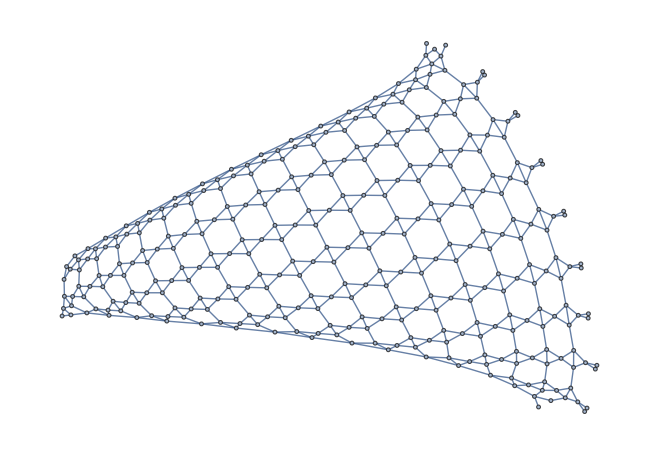

```mathematica
{IC[
IC[{1,12 i k-5 i-12 k+7},{i,1,2}],
IC[{3 j+12 k-10,3 j+12 k-9},{1,2,3},{2 j+12 k-7,2 j+12 k-6},{1,2},{2 j+12 k-9,2 j+12 k-7},IC[IC[{1,2},2],{2 j+12 k-8,2 j+12 k-7},4 k-3],{j,1,2}],

IC[{1,12 i k-2 i-12 k+4},{i,1,2}],
IC[{3 j+12 k-7,3 j+12 k-6},{1,2,3},{2 j+12 k-4,2 j+12 k-3},{1,2},{2 j+12 k-6,2 j+12 k-4},IC[IC[{1,2},2],{2 j+12 k-5,2 j+12 k-4},4 k-2],{j,1,2}],

IC[{1,12 i k+i-12 k+1},{i,1,2}],
IC[{3 j+12 k-4,3 j+12 k-3},{1,2,3},{2 j+12 k-1,2 j+12 k},{1,2},{2 j+12 k-3,2 j+12 k-1},IC[IC[{1,2},2],{2 j+12 k-2,2 j+12 k-1},4 k-1],{j,1,2}],

IC[{1,12 i k+4 i-12 k-2},{i,1,2}],
IC[{3 j+12 k-1,3 j+12 k},{1,2,3},{2 j+12 k+2,2 j+12 k+3},{1,2},{2 j+12 k,2 j+12 k+2},IC[IC[{1,2},2],{2 j+12 k+1,2 j+12 k+2},4 k],{j,1,2}],{k,1,2}]} /.IC->IndexedConcatenate //ExpandAll//FromNetDifferenceSets//GraphPlot
```

```mathematica
FindSequenceFunction[{12 i k-5 i-12 k+7,12 i k-2 i-12 k+4,12 i k+i-12 k+1,12 i k+4 i-12 k-2},n]
```

10-8 i-12 k+12 i k-3 n+3 i n

```mathematica
FindSequenceFunction[{3 j+12 k-10,3 j+12 k-7,3 j+12 k-4,3 j+12 k-1},n]
```

-13+3 j+12 k+3 n

```mathematica
FindSequenceFunction[{2 j+12 k-7,2 j+12 k-4,2 j+12 k-1,2 j+12 k+2},n]
```

-10+2 j+12 k+3 n

```mathematica
FindSequenceFunction[{2 j+12 k-9,2 j+12 k-6,2 j+12 k-3,2 j+12 k},n]
```

-12+2 j+12 k+3 n

```mathematica
FindSequenceFunction[{2 j+12 k-8,2 j+12 k-5,2 j+12 k-2,2 j+12 k+1},n]
```

-11+2 j+12 k+3 n

```mathematica
{IC[
IC[
IC[{1,10-8 i-12 k+12 i k-3 n+3 i n},{i,1,2}],
IC[{-13+3 j+12 k+3 n,-12+3 j+12 k+3 n},{1,2,3},{2 j+12 k-7,2 j+12 k-6},{1,2},{-12+2 j+12 k+3 n,-10+2 j+12 k+3 n},IC[IC[{1,2},2],{-11+2 j+12 k+3 n,-10+2 j+12 k+3 n},4 k-3],{j,1,2}],
{n,1,4}],
{k,1,2}]} /.IC->IndexedConcatenate//ExpandAll
```

{{1,2},{1,9},{5,6},{1,2,3},{7,8},{1,2},{5,7},{1,2},{1,2},{6,7},{8,9},{1,2,3},{9,10},{1,2},{7,9},{1,2},{1,2},{8,9},{1,2},{1,12},{8,9},{1,2,3},{7,8},{1,2},{8,10},{1,2},{1,2},{9,10},{11,12},{1,2,3},{9,10},{1,2},{10,12},{1,2},{1,2},{11,12},{1,2},{1,15},{11,12},{1,2,3},{7,8},{1,2},{11,13},{1,2},{1,2},{12,13},{14,15},{1,2,3},{9,10},{1,2},{13,15},{1,2},{1,2},{14,15},{1,2},{1,18},{14,15},{1,2,3},{7,8},{1,2},{14,16},{1,2},{1,2},{15,16},{17,18},{1,2,3},{9,10},{1,2},{16,18},{1,2},{1,2},{17,18},{1,2},{1,21},{17,18},{1,2,3},{19,20},{1,2},{17,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{20,21},{1,2,3},{21,22},{1,2},{19,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,24},{20,21},{1,2,3},{19,20},{1,2},{20,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{23,24},{1,2,3},{21,22},{1,2},{22,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,27},{23,24},{1,2,3},{19,20},{1,2},{23,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{26,27},{1,2,3},{21,22},{1,2},{25,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,30},{26,27},{1,2,3},{19,20},{1,2},{26,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{29,30},{1,2,3},{21,22},{1,2},{28,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30}}

```mathematica
SequencePosition[nds01,%52]
```

{}

```mathematica
GraphPlot3D[FromNetDifferenceSets[%48]]
```

```mathematica
SequencePosition[nds01,%44]
```

{}

```mathematica
{IndexedConcatenate[IndexedConcatenate[{1, 7 - 5*i + 12*(-1 + i)*k}, {i, 1, 2}], IndexedConcatenate[{-10 + 3*j + 12*k, 3*(-3 + j + 4*k)}, {1, 2, 3}, {-7 + 2*j + 12*k, 2*(-3 + j + 6*k)}, {1, 2}, 
   {-9 + 2*j + 12*k, -7 + 2*j + 12*k}, IndexedConcatenate[IndexedConcatenate[{1, 2}, 2], {2*(-4 + j + 6*k), -7 + 2*j + 12*k}, -3 + 4*k], {j, 1, 2}], IndexedConcatenate[{1, 2 + 2*(-1 + i)*(-1 + 6*k)}, {i, 1, 2}], 
  IndexedConcatenate[{-7 + 3*j + 12*k, 3*(-2 + j + 4*k)}, {1, 2, 3}, {2*(-2 + j + 6*k), -3 + 2*j + 12*k}, {1, 2}, {2*(-3 + j + 6*k), 2*(-2 + j + 6*k)}, 
   IndexedConcatenate[IndexedConcatenate[{1, 2}, 2], {-5 + 2*j + 12*k, 2*(-2 + j + 6*k)}, -2 + 4*k], {j, 1, 2}], IndexedConcatenate[{1, 1 + i + 12*(-1 + i)*k}, {i, 1, 2}], 
  IndexedConcatenate[{-4 + 3*j + 12*k, 3*(-1 + j + 4*k)}, {1, 2, 3}, {-1 + 2*j + 12*k, 2*(j + 6*k)}, {1, 2}, {-3 + 2*j + 12*k, -1 + 2*j + 12*k}, 
   IndexedConcatenate[IndexedConcatenate[{1, 2}, 2], {2*(-1 + j + 6*k), -1 + 2*j + 12*k}, -1 + 4*k], {j, 1, 2}], IndexedConcatenate[{1, 2 + 4*(-1 + i)*(1 + 3*k)}, {i, 1, 2}], 
  IndexedConcatenate[{-1 + 3*j + 12*k, 3*(j + 4*k)}, {1, 2, 3}, {2*(1 + j + 6*k), 3 + 2*j + 12*k}, {1, 2}, {2*(j + 6*k), 2*(1 + j + 6*k)}, 
   IndexedConcatenate[IndexedConcatenate[{1, 2}, 2], {1 + 2*j + 12*k, 2*(1 + j + 6*k)}, 4*k], {j, 1, 2}], {k, 1, 8}]}
```

```mathematica
{€_(k⊨1)^8[
€_(i⊨1)^2[{1,7-5 i+12 (-1+i) k}],
€_(j⊨1)^2[{-10+3 j+12 k,3 (-3+j+4 k)},{1,2,3},{-7+2 j+12 k,2 (-3+j+6 k)},{1,2},{-9+2 j+12 k,-7+2 j+12 k},€^(-3+4 k)[€^2[{1,2}],{2 (-4+j+6 k),-7+2 j+12 k}]],€_(i⊨1)^2[{1,2+2 (-1+i) (-1+6 k)}],
€_(j⊨1)^2[{-7+3 j+12 k,3 (-2+j+4 k)},{1,2,3},{2 (-2+j+6 k),-3+2 j+12 k},{1,2},{2 (-3+j+6 k),2 (-2+j+6 k)},€^(-2+4 k)[€^2[{1,2}],{-5+2 j+12 k,2 (-2+j+6 k)}]],€_(i⊨1)^2[{1,1+i+12 (-1+i) k}],
€_(j⊨1)^2[{-4+3 j+12 k,3 (-1+j+4 k)},{1,2,3},{-1+2 j+12 k,2 (j+6 k)},{1,2},{-3+2 j+12 k,-1+2 j+12 k},€^(-1+4 k)[€^2[{1,2}],{2 (-1+j+6 k),-1+2 j+12 k}]],€_(i⊨1)^2[{1,2+4 (-1+i) (1+3 k)}],
€_(j⊨1)^2[{-1+3 j+12 k,3 (j+4 k)},{1,2,3},{2 (1+j+6 k),3+2 j+12 k},{1,2},{2 (j+6 k),2 (1+j+6 k)},€^(4 k)[€^2[{1,2}],{1+2 j+12 k,2 (1+j+6 k)}]]
]}
```

```mathematica
SequencePosition[nds01,
{IndexedConcatenate[IndexedConcatenate[{1, 7 - 5*i + 12*(-1 + i)*k}, {i, 1, 2}], IndexedConcatenate[{-10 + 3*j + 12*k, 3*(-3 + j + 4*k)}, {1, 2, 3}, {-7 + 2*j + 12*k, 2*(-3 + j + 6*k)}, {1, 2}, 
   {-9 + 2*j + 12*k, -7 + 2*j + 12*k}, IndexedConcatenate[IndexedConcatenate[{1, 2}, 2], {2*(-4 + j + 6*k), -7 + 2*j + 12*k}, -3 + 4*k], {j, 1, 2}], IndexedConcatenate[{1, 2 + 2*(-1 + i)*(-1 + 6*k)}, {i, 1, 2}], 
  IndexedConcatenate[{-7 + 3*j + 12*k, 3*(-2 + j + 4*k)}, {1, 2, 3}, {2*(-2 + j + 6*k), -3 + 2*j + 12*k}, {1, 2}, {2*(-3 + j + 6*k), 2*(-2 + j + 6*k)}, 
   IndexedConcatenate[IndexedConcatenate[{1, 2}, 2], {-5 + 2*j + 12*k, 2*(-2 + j + 6*k)}, -2 + 4*k], {j, 1, 2}], IndexedConcatenate[{1, 1 + i + 12*(-1 + i)*k}, {i, 1, 2}], 
  IndexedConcatenate[{-4 + 3*j + 12*k, 3*(-1 + j + 4*k)}, {1, 2, 3}, {-1 + 2*j + 12*k, 2*(j + 6*k)}, {1, 2}, {-3 + 2*j + 12*k, -1 + 2*j + 12*k}, 
   IndexedConcatenate[IndexedConcatenate[{1, 2}, 2], {2*(-1 + j + 6*k), -1 + 2*j + 12*k}, -1 + 4*k], {j, 1, 2}], IndexedConcatenate[{1, 2 + 4*(-1 + i)*(1 + 3*k)}, {i, 1, 2}], 
  IndexedConcatenate[{-1 + 3*j + 12*k, 3*(j + 4*k)}, {1, 2, 3}, {2*(1 + j + 6*k), 3 + 2*j + 12*k}, {1, 2}, {2*(j + 6*k), 2*(1 + j + 6*k)}, 
   IndexedConcatenate[IndexedConcatenate[{1, 2}, 2], {1 + 2*j + 12*k, 2*(1 + j + 6*k)}, 4*k], {j, 1, 2}], {k, 1, 8}]}//ExpandAll
   ]
```

{{16,3567}}

{{1, 2}, {1, -3}, {-7, -6}, {1, 2, 3}, {-5, -4}, {1, 2}, {-7, -5}, {-4, -3}, {1, 2, 3}, {-3, -2}, {1, 2}, {-5, -3}, {1, 2}, {1, 0}, {-4, -3}, {1, 2, 3}, {-2, -1}, {1, 2}, {-4, -2}, {-1, 0}, {1, 2, 3}, {0, 1}, {1, 2}, {-2, 0}, {1, 2}, {1, 3}, {-1, 0}, {1, 2, 3}, {1, 2}, {1, 2}, {-1, 1}, {2, 3}, {1, 2, 3}, {3, 4}, {1, 2}, {1, 3}, {1, 2}, {1, 6}, {2, 3}, {1, 2, 3}, {4, 5}, {1, 2}, {2, 4}, {5, 6}, {1, 2, 3}, {6, 7}, {1, 2}, {4, 6}}

```mathematica
rsl01[[6;;13]]/.{n$1->i,n$2->j,n$3->k,n$4->m}//ExpandAll
```

{{1,2,3},{4,5},{1,2},{2,4},{5,6},{1,2,3},{6,7},{1,2},{4,6}}

{{1, 2, 4}, {1, 2}, {1, 2, 3}, {3, 4}, {1, 6}, {1, 3}, {1, 2, 3}, {4, 5}, {1, 2}, {2, 4}, {5, 6}, {1, 2, 3}, {6, 7}, {1, 2}, {4, 6}}

```mathematica
{IndexedConcatenate[IndexedConcatenate[{1, 7 - 5*i + 12*(-1 + i)*k}, {i, 1, 2}], IndexedConcatenate[{-10 + 3*j + 12*k, 3*(-3 + j + 4*k)}, {1, 2, 3}, {-7 + 2*j + 12*k, 2*(-3 + j + 6*k)}, {1, 2}, 
   {-9 + 2*j + 12*k, -7 + 2*j + 12*k}, IndexedConcatenate[IndexedConcatenate[{1, 2}, 2], {2*(-4 + j + 6*k), -7 + 2*j + 12*k}, -3 + 4*k], {j, 1, 2}], IndexedConcatenate[{1, 2 + 2*(-1 + i)*(-1 + 6*k)}, {i, 1, 2}], 
  IndexedConcatenate[{-7 + 3*j + 12*k, 3*(-2 + j + 4*k)}, {1, 2, 3}, {2*(-2 + j + 6*k), -3 + 2*j + 12*k}, {1, 2}, {2*(-3 + j + 6*k), 2*(-2 + j + 6*k)}, 
   IndexedConcatenate[IndexedConcatenate[{1, 2}, 2], {-5 + 2*j + 12*k, 2*(-2 + j + 6*k)}, -2 + 4*k], {j, 1, 2}], IndexedConcatenate[{1, 1 + i + 12*(-1 + i)*k}, {i, 1, 2}], 
  IndexedConcatenate[{-4 + 3*j + 12*k, 3*(-1 + j + 4*k)}, {1, 2, 3}, {-1 + 2*j + 12*k, 2*(j + 6*k)}, {1, 2}, {-3 + 2*j + 12*k, -1 + 2*j + 12*k}, 
   IndexedConcatenate[IndexedConcatenate[{1, 2}, 2], {2*(-1 + j + 6*k), -1 + 2*j + 12*k}, -1 + 4*k], {j, 1, 2}], IndexedConcatenate[{1, 2 + 4*(-1 + i)*(1 + 3*k)}, {i, 1, 2}], 
  IndexedConcatenate[{-1 + 3*j + 12*k, 3*(j + 4*k)}, {1, 2, 3}, {2*(1 + j + 6*k), 3 + 2*j + 12*k}, {1, 2}, {2*(j + 6*k), 2*(1 + j + 6*k)}, 
   IndexedConcatenate[IndexedConcatenate[{1, 2}, 2], {1 + 2*j + 12*k, 2*(1 + j + 6*k)}, 4*k], {j, 1, 2}], {k, 1, 0}]}//ExpandAll
```

```mathematica
{{1,2,4},{1,2},{1,2,3},{3,4},€_(n$1⊨1)^2[{1,6-3 (n$1-1)}],{1,2,3},{4,5},{1,2},€_(n$1⊨1)^2[{3 (n$1-1)+2,2 (n$1-1)+4}],{1,2,3},{6,7},{1,2},{4,6},€_(n$3⊨1)^8[€_(n$1⊨1)^2[{1,-5 n$1+12 (n$1-1) n$3+7}],€_(n$2⊨1)^2[{3 n$2+12 n$3-10,3 (n$2+4 n$3-3)},{1,2,3},{2 n$2+12 n$3-7,2 (n$2+6 n$3-3)},{1,2},{2 n$2+12 n$3-9,2 n$2+12 n$3-7},€^(4 n$3-3)[€^2[{1,2}],{2 (n$2+6 n$3-4),2 n$2+12 n$3-7}]],€_(n$1⊨1)^2[{1,2 (n$1-1) (6 n$3-1)+2}],€_(n$2⊨1)^2[{3 n$2+12 n$3-7,3 (n$2+4 n$3-2)},{1,2,3},{2 (n$2+6 n$3-2),2 n$2+12 n$3-3},{1,2},{2 (n$2+6 n$3-3),2 (n$2+6 n$3-2)},€^(4 n$3-2)[€^2[{1,2}],{2 n$2+12 n$3-5,2 (n$2+6 n$3-2)}]],€_(n$1⊨1)^2[{1,n$1+12 (n$1-1) n$3+1}],€_(n$2⊨1)^2[{3 n$2+12 n$3-4,3 (n$2+4 n$3-1)},{1,2,3},{2 n$2+12 n$3-1,2 (n$2+6 n$3)},{1,2},{2 n$2+12 n$3-3,2 n$2+12 n$3-1},€^(4 n$3-1)[€^2[{1,2}],{2 (n$2+6 n$3-1),2 n$2+12 n$3-1}]],€_(n$1⊨1)^2[{1,4 (n$1-1) (3 n$3+1)+2}],€_(n$2⊨1)^2[{3 n$2+12 n$3-1,3 (n$2+4 n$3)},{1,2,3},{2 (n$2+6 n$3+1),2 n$2+12 n$3+3},{1,2},{2 (n$2+6 n$3),2 (n$2+6 n$3+1)},€^(4 n$3)[€^2[{1,2}],{2 n$2+12 n$3+1,2 (n$2+6 n$3+1)}]]]}
```

```mathematica
rsl01[[5;;5]]//ExpandAll
```

{{1,6},{1,3}}

```mathematica
Position[nds01,rsl01[[5]]//ExpandAll]
```

{{5}}

```mathematica
rsl01[[14;;14]]/.{n$1->i,n$2->j,n$3->k,IndexedConcatenate->IC}//ExpandAll
```

```mathematica
{IC[
IC[{1,7-5 i-12 k+12 i k},{i,1,2}],
IC[{-10+3 j+12 k,-9+3 j+12 k},{1,2,3},{-7+2 j+12 k,-6+2 j+12 k},{1,2},{-9+2 j+12 k,-7+2 j+12 k},IC[IC[{1,2},2],{-8+2 j+12 k,-7+2 j+12 k},-3+4 k],{j,1,2}],

IC[{1,4-2 i-12 k+12 i k},{i,1,2}],
IC[{-7+3 j+12 k,-6+3 j+12 k},{1,2,3},{-4+2 j+12 k,-3+2 j+12 k},{1,2},{-6+2 j+12 k,-4+2 j+12 k},
IC[IC[{1,2},2],{-5+2 j+12 k,-4+2 j+12 k},-2+4 k],{j,1,2}],

IC[{1,1+i-12 k+12 i k},{i,1,2}],
IC[{-4+3 j+12 k,-3+3 j+12 k},{1,2,3},{-1+2 j+12 k,2 j+12 k},{1,2},{-3+2 j+12 k,-1+2 j+12 k},
IC[IC[{1,2},2],{-2+2 j+12 k,-1+2 j+12 k},-1+4 k],{j,1,2}],

IC[{1,-2+4 i-12 k+12 i k},{i,1,2}],
IC[{-1+3 j+12 k,3 j+12 k},{1,2,3},{2+2 j+12 k,3+2 j+12 k},{1,2},{2 j+12 k,2+2 j+12 k},
IC[IC[{1,2},2],{1+2 j+12 k,2+2 j+12 k},4 k],{j,1,2}],
{k,1,5}
]}
```

```mathematica
{IC[
IndexedConcatenate[
IC[{1,7-3m-5 i+3m i-12 k+12 i k},{i,1,2}],
IC[{-10+3m+3 j+12 k,-9+3m+3 j+12 k},{1,2,3},{-7+3m+2 j+12 k,-6+3m+2 j+12 k},{1,2},{-9+3m+2 j+12 k,-7+3m+2 j+12 k},IC[IC[{1,2},2],{-8+3m+2 j+12 k,-7+3m+2 j+12 k},-3+m+4 k],{j,1,2}],
{m,0,3}],
{k,1,5}
]}//Expand
```

{IC[IC[{1,7-5 i-12 k+12 i k},{i,1,2}],IC[{-10+3 j+12 k,-9+3 j+12 k},{1,2,3},{-7+2 j+12 k,-6+2 j+12 k},{1,2},{-9+2 j+12 k,-7+2 j+12 k},IC[IC[{1,2},2],{-8+2 j+12 k,-7+2 j+12 k},-3+4 k],{j,1,2}],IC[{1,4-2 i-12 k+12 i k},{i,1,2}],IC[{-7+3 j+12 k,-6+3 j+12 k},{1,2,3},{-4+2 j+12 k,-3+2 j+12 k},{1,2},{-6+2 j+12 k,-4+2 j+12 k},IC[IC[{1,2},2],{-5+2 j+12 k,-4+2 j+12 k},-2+4 k],{j,1,2}],IC[{1,1+i-12 k+12 i k},{i,1,2}],IC[{-4+3 j+12 k,-3+3 j+12 k},{1,2,3},{-1+2 j+12 k,2 j+12 k},{1,2},{-3+2 j+12 k,-1+2 j+12 k},IC[IC[{1,2},2],{-2+2 j+12 k,-1+2 j+12 k},-1+4 k],{j,1,2}],IC[{1,-2+4 i-12 k+12 i k},{i,1,2}],IC[{-1+3 j+12 k,3 j+12 k},{1,2,3},{2+2 j+12 k,3+2 j+12 k},{1,2},{2 j+12 k,2+2 j+12 k},IC[IC[{1,2},2],{1+2 j+12 k,2+2 j+12 k},4 k],{j,1,2}],{k,1,5}]}

```mathematica
%91==%37
```

True

```mathematica
{IC[
IC[
IC[{1,7-3m-5 i+3m i-12 k+12 i k},{i,1,2}],
IC[{-10+3m+3 j+12 k,-9+3m+3 j+12 k},{1,2,3},{-7+3m+2 j+12 k,-6+3m+2 j+12 k},{1,2},{-9+3m+2 j+12 k,-7+3m+2 j+12 k},IC[IC[{1,2},2],{-8+3m+2 j+12 k,-7+3m+2 j+12 k},-3+m+4 k],{j,1,2}],
{m,0,3}],
{k,1,5}
]} /. IC->IndexedConcatenate
```

{€_(k⊨1)^5[€_(m⊨0)^3[€_(i⊨1)^2[{1,7-5 i-12 k+12 i k-3 m+3 i m}],€_(j⊨1)^2[{-10+3 j+12 k+3 m,-9+3 j+12 k+3 m},{1,2,3},{-7+2 j+12 k+3 m,-6+2 j+12 k+3 m},{1,2},{-9+2 j+12 k+3 m,-7+2 j+12 k+3 m},€^(-3+4 k+m)[€^2[{1,2}],{-8+2 j+12 k+3 m,-7+2 j+12 k+3 m}]]]]}

```mathematica
%//ExpandAll
```

{{1,2},{1,9},{5,6},{1,2,3},{7,8},{1,2},{5,7},{1,2},{1,2},{6,7},{8,9},{1,2,3},{9,10},{1,2},{7,9},{1,2},{1,2},{8,9},{1,2},{1,12},{8,9},{1,2,3},{10,11},{1,2},{8,10},{1,2},{1,2},{9,10},{1,2},{1,2},{9,10},{11,12},{1,2,3},{12,13},{1,2},{10,12},{1,2},{1,2},{11,12},{1,2},{1,2},{11,12},{1,2},{1,15},{11,12},{1,2,3},{13,14},{1,2},{11,13},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{14,15},{1,2,3},{15,16},{1,2},{13,15},{1,2},{1,2},{14,15},{1,2},{1,2},{14,15},{1,2},{1,2},{14,15},{1,2},{1,18},{14,15},{1,2,3},{16,17},{1,2},{14,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{17,18},{1,2,3},{18,19},{1,2},{16,18},{1,2},{1,2},{17,18},{1,2},{1,2},{17,18},{1,2},{1,2},{17,18},{1,2},{1,2},{17,18},{1,2},{1,21},{17,18},{1,2,3},{19,20},{1,2},{17,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{20,21},{1,2,3},{21,22},{1,2},{19,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,24},{20,21},{1,2,3},{22,23},{1,2},{20,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{23,24},{1,2,3},{24,25},{1,2},{22,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,27},{23,24},{1,2,3},{25,26},{1,2},{23,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{26,27},{1,2,3},{27,28},{1,2},{25,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,30},{26,27},{1,2,3},{28,29},{1,2},{26,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{29,30},{1,2,3},{30,31},{1,2},{28,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,33},{29,30},{1,2,3},{31,32},{1,2},{29,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{32,33},{1,2,3},{33,34},{1,2},{31,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,36},{32,33},{1,2,3},{34,35},{1,2},{32,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{35,36},{1,2,3},{36,37},{1,2},{34,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,39},{35,36},{1,2,3},{37,38},{1,2},{35,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{38,39},{1,2,3},{39,40},{1,2},{37,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,42},{38,39},{1,2,3},{40,41},{1,2},{38,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{41,42},{1,2,3},{42,43},{1,2},{40,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,45},{41,42},{1,2,3},{43,44},{1,2},{41,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{44,45},{1,2,3},{45,46},{1,2},{43,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,48},{44,45},{1,2,3},{46,47},{1,2},{44,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{47,48},{1,2,3},{48,49},{1,2},{46,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,51},{47,48},{1,2,3},{49,50},{1,2},{47,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{50,51},{1,2,3},{51,52},{1,2},{49,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,54},{50,51},{1,2,3},{52,53},{1,2},{50,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{53,54},{1,2,3},{54,55},{1,2},{52,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,57},{53,54},{1,2,3},{55,56},{1,2},{53,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{56,57},{1,2,3},{57,58},{1,2},{55,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,60},{56,57},{1,2,3},{58,59},{1,2},{56,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{59,60},{1,2,3},{60,61},{1,2},{58,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,63},{59,60},{1,2,3},{61,62},{1,2},{59,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{62,63},{1,2,3},{63,64},{1,2},{61,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,66},{62,63},{1,2,3},{64,65},{1,2},{62,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{65,66},{1,2,3},{66,67},{1,2},{64,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66}}

```mathematica
nds01
```

{{1,2,4},{1,2},{1,2,3},{3,4},{1,6},{1,3},{1,2,3},{4,5},{1,2},{2,4},{5,6},{1,2,3},{6,7},{1,2},{4,6},{1,2},{1,9},{5,6},{1,2,3},{7,8},{1,2},{5,7},{1,2},{1,2},{6,7},{8,9},{1,2,3},{9,10},{1,2},{7,9},{1,2},{1,2},{8,9},{1,2},{1,12},{8,9},{1,2,3},{10,11},{1,2},{8,10},{1,2},{1,2},{9,10},{1,2},{1,2},{9,10},{11,12},{1,2,3},{12,13},{1,2},{10,12},{1,2},{1,2},{11,12},{1,2},{1,2},{11,12},{1,2},{1,15},{11,12},{1,2,3},{13,14},{1,2},{11,13},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{14,15},{1,2,3},{15,16},{1,2},{13,15},{1,2},{1,2},{14,15},{1,2},{1,2},{14,15},{1,2},{1,2},{14,15},{1,2},{1,18},{14,15},{1,2,3},{16,17},{1,2},{14,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{17,18},{1,2,3},{18,19},{1,2},{16,18},{1,2},{1,2},{17,18},{1,2},{1,2},{17,18},{1,2},{1,2},{17,18},{1,2},{1,2},{17,18},{1,2},{1,21},{17,18},{1,2,3},{19,20},{1,2},{17,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{20,21},{1,2,3},{21,22},{1,2},{19,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,24},{20,21},{1,2,3},{22,23},{1,2},{20,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{23,24},{1,2,3},{24,25},{1,2},{22,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,27},{23,24},{1,2,3},{25,26},{1,2},{23,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{26,27},{1,2,3},{27,28},{1,2},{25,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,30},{26,27},{1,2,3},{28,29},{1,2},{26,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{29,30},{1,2,3},{30,31},{1,2},{28,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,33},{29,30},{1,2,3},{31,32},{1,2},{29,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{32,33},{1,2,3},{33,34},{1,2},{31,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,36},{32,33},{1,2,3},{34,35},{1,2},{32,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{35,36},{1,2,3},{36,37},{1,2},{34,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,39},{35,36},{1,2,3},{37,38},{1,2},{35,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{38,39},{1,2,3},{39,40},{1,2},{37,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,42},{38,39},{1,2,3},{40,41},{1,2},{38,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{41,42},{1,2,3},{42,43},{1,2},{40,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,45},{41,42},{1,2,3},{43,44},{1,2},{41,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{44,45},{1,2,3},{45,46},{1,2},{43,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,48},{44,45},{1,2,3},{46,47},{1,2},{44,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{47,48},{1,2,3},{48,49},{1,2},{46,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,51},{47,48},{1,2,3},{49,50},{1,2},{47,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{50,51},{1,2,3},{51,52},{1,2},{49,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,54},{50,51},{1,2,3},{52,53},{1,2},{50,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{53,54},{1,2,3},{54,55},{1,2},{52,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,57},{53,54},{1,2,3},{55,56},{1,2},{53,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{56,57},{1,2,3},{57,58},{1,2},{55,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,60},{56,57},{1,2,3},{58,59},{1,2},{56,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{59,60},{1,2,3},{60,61},{1,2},{58,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,63},{59,60},{1,2,3},{61,62},{1,2},{59,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{62,63},{1,2,3},{63,64},{1,2},{61,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,66},{62,63},{1,2,3},{64,65},{1,2},{62,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{65,66},{1,2,3},{66,67},{1,2},{64,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,69},{65,66},{1,2,3},{67,68},{1,2},{65,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{68,69},{1,2,3},{69,70},{1,2},{67,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,72},{68,69},{1,2,3},{70,71},{1,2},{68,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{71,72},{1,2,3},{72,73},{1,2},{70,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,75},{71,72},{1,2,3},{73,74},{1,2},{71,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{74,75},{1,2,3},{75,76},{1,2},{73,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74,75},{1,2},{1,2},{74},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1},{},{1,2,3},{},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2}}

```mathematica
Position[nds01,%98[[51;;55]]]
```

{}

```mathematica
rsl01[[14;;14]]/.{n$1->i,n$2->j,n$3->k}//ExpandAll
```

{{1,2},{1,9},{5,6},{1,2,3},{7,8},{1,2},{5,7},{1,2},{1,2},{6,7},{8,9},{1,2,3},{9,10},{1,2},{7,9},{1,2},{1,2},{8,9},{1,2},{1,12},{8,9},{1,2,3},{10,11},{1,2},{8,10},{1,2},{1,2},{9,10},{1,2},{1,2},{9,10},{11,12},{1,2,3},{12,13},{1,2},{10,12},{1,2},{1,2},{11,12},{1,2},{1,2},{11,12},{1,2},{1,15},{11,12},{1,2,3},{13,14},{1,2},{11,13},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{14,15},{1,2,3},{15,16},{1,2},{13,15},{1,2},{1,2},{14,15},{1,2},{1,2},{14,15},{1,2},{1,2},{14,15},{1,2},{1,18},{14,15},{1,2,3},{16,17},{1,2},{14,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{17,18},{1,2,3},{18,19},{1,2},{16,18},{1,2},{1,2},{17,18},{1,2},{1,2},{17,18},{1,2},{1,2},{17,18},{1,2},{1,2},{17,18},{1,2},{1,21},{17,18},{1,2,3},{19,20},{1,2},{17,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{20,21},{1,2,3},{21,22},{1,2},{19,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,24},{20,21},{1,2,3},{22,23},{1,2},{20,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{23,24},{1,2,3},{24,25},{1,2},{22,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,27},{23,24},{1,2,3},{25,26},{1,2},{23,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{26,27},{1,2,3},{27,28},{1,2},{25,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,30},{26,27},{1,2,3},{28,29},{1,2},{26,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{29,30},{1,2,3},{30,31},{1,2},{28,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,33},{29,30},{1,2,3},{31,32},{1,2},{29,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{32,33},{1,2,3},{33,34},{1,2},{31,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,36},{32,33},{1,2,3},{34,35},{1,2},{32,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{35,36},{1,2,3},{36,37},{1,2},{34,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,39},{35,36},{1,2,3},{37,38},{1,2},{35,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{38,39},{1,2,3},{39,40},{1,2},{37,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,42},{38,39},{1,2,3},{40,41},{1,2},{38,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{41,42},{1,2,3},{42,43},{1,2},{40,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,45},{41,42},{1,2,3},{43,44},{1,2},{41,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{44,45},{1,2,3},{45,46},{1,2},{43,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,48},{44,45},{1,2,3},{46,47},{1,2},{44,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{47,48},{1,2,3},{48,49},{1,2},{46,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,51},{47,48},{1,2,3},{49,50},{1,2},{47,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{50,51},{1,2,3},{51,52},{1,2},{49,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,54},{50,51},{1,2,3},{52,53},{1,2},{50,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{53,54},{1,2,3},{54,55},{1,2},{52,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,57},{53,54},{1,2,3},{55,56},{1,2},{53,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{56,57},{1,2,3},{57,58},{1,2},{55,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,60},{56,57},{1,2,3},{58,59},{1,2},{56,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{59,60},{1,2,3},{60,61},{1,2},{58,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,63},{59,60},{1,2,3},{61,62},{1,2},{59,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{62,63},{1,2,3},{63,64},{1,2},{61,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,66},{62,63},{1,2,3},{64,65},{1,2},{62,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{65,66},{1,2,3},{66,67},{1,2},{64,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66}}

```mathematica
Position[nds01,%]
```

{}

```mathematica
nds01[[1;;1878]]
```

{{1,2,4},{1,2},{1,2,3},{3,4},{1,6},{1,3},{1,2,3},{4,5},{1,2},{2,4},{5,6},{1,2,3},{6,7},{1,2},{4,6},{1,2},{1,9},{5,6},{1,2,3},{7,8},{1,2},{5,7},{1,2},{1,2},{6,7},{8,9},{1,2,3},{9,10},{1,2},{7,9},{1,2},{1,2},{8,9},{1,2},{1,12},{8,9},{1,2,3},{10,11},{1,2},{8,10},{1,2},{1,2},{9,10},{1,2},{1,2},{9,10},{11,12},{1,2,3},{12,13},{1,2},{10,12},{1,2},{1,2},{11,12},{1,2},{1,2},{11,12},{1,2},{1,15},{11,12},{1,2,3},{13,14},{1,2},{11,13},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{14,15},{1,2,3},{15,16},{1,2},{13,15},{1,2},{1,2},{14,15},{1,2},{1,2},{14,15},{1,2},{1,2},{14,15},{1,2},{1,18},{14,15},{1,2,3},{16,17},{1,2},{14,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{17,18},{1,2,3},{18,19},{1,2},{16,18},{1,2},{1,2},{17,18},{1,2},{1,2},{17,18},{1,2},{1,2},{17,18},{1,2},{1,2},{17,18},{1,2},{1,21},{17,18},{1,2,3},{19,20},{1,2},{17,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{20,21},{1,2,3},{21,22},{1,2},{19,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,24},{20,21},{1,2,3},{22,23},{1,2},{20,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{23,24},{1,2,3},{24,25},{1,2},{22,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,27},{23,24},{1,2,3},{25,26},{1,2},{23,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{26,27},{1,2,3},{27,28},{1,2},{25,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,30},{26,27},{1,2,3},{28,29},{1,2},{26,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{29,30},{1,2,3},{30,31},{1,2},{28,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,33},{29,30},{1,2,3},{31,32},{1,2},{29,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{32,33},{1,2,3},{33,34},{1,2},{31,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,36},{32,33},{1,2,3},{34,35},{1,2},{32,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{35,36},{1,2,3},{36,37},{1,2},{34,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,39},{35,36},{1,2,3},{37,38},{1,2},{35,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{38,39},{1,2,3},{39,40},{1,2},{37,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,2},{38,39},{1,2},{1,42},{38,39},{1,2,3},{40,41},{1,2},{38,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{41,42},{1,2,3},{42,43},{1,2},{40,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,2},{41,42},{1,2},{1,45},{41,42},{1,2,3},{43,44},{1,2},{41,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{44,45},{1,2,3},{45,46},{1,2},{43,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,2},{44,45},{1,2},{1,48},{44,45},{1,2,3},{46,47},{1,2},{44,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{47,48},{1,2,3},{48,49},{1,2},{46,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,2},{47,48},{1,2},{1,51},{47,48},{1,2,3},{49,50},{1,2},{47,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{50,51},{1,2,3},{51,52},{1,2},{49,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,2},{50,51},{1,2},{1,54},{50,51},{1,2,3},{52,53},{1,2},{50,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{53,54},{1,2,3},{54,55},{1,2},{52,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,2},{53,54},{1,2},{1,57},{53,54},{1,2,3},{55,56},{1,2},{53,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{1,2},{1,2},{54,55},{56,57},{1,2,3},{57,58},{1,2},{55,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,2},{56,57},{1,2},{1,60},{56,57},{1,2,3},{58,59},{1,2},{56,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{1,2},{1,2},{57,58},{59,60},{1,2,3},{60,61},{1,2},{58,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,2},{59,60},{1,2},{1,63},{59,60},{1,2,3},{61,62},{1,2},{59,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{1,2},{1,2},{60,61},{62,63},{1,2,3},{63,64},{1,2},{61,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,2},{62,63},{1,2},{1,66},{62,63},{1,2,3},{64,65},{1,2},{62,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{1,2},{1,2},{63,64},{65,66},{1,2,3},{66,67},{1,2},{64,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,2},{65,66},{1,2},{1,69},{65,66},{1,2,3},{67,68},{1,2},{65,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{1,2},{1,2},{66,67},{68,69},{1,2,3},{69,70},{1,2},{67,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,2},{68,69},{1,2},{1,72},{68,69},{1,2,3},{70,71},{1,2},{68,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{1,2},{1,2},{69,70},{71,72},{1,2,3},{72,73},{1,2},{70,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,2},{71,72},{1,2},{1,75},{71,72},{1,2,3},{73,74},{1,2},{71,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{1,2},{1,2},{72,73},{74,75},{1,2,3},{75,76},{1,2},{73,75}}

```mathematica
$debug=True;
```

```mathematica
ReduceSetList[nds01[[1;;1878]]]
```

$Aborted

```mathematica
nds01[[1;;148]]
```

```mathematica
{{1,2,4},{1,2},

{1,2,3},{3,4},{1,6},{1,3},

{1,2,3},{4,5},{1,2},{2,4},{5,6},

{1,2,3},{6,7},


{1,2},{4,6},



{1,2},{1,9},

{5,6},{1,2,3},{7,8},{1,2},{5,7},

{1,2},{1,2},{6,7},

{8,9},{1,2,3},{9,10},{1,2},{7,9},


{1,2},{1,2},{8,9},
{1,2},{1,12},{8,9},

{1,2,3},{10,11},{1,2},{8,10},

{1,2},{1,2},{9,10},
{1,2},{1,2},{9,10},{11,12},

{1,2,3},{12,13},{1,2},{10,12},

{1,2},{1,2},{11,12},
{1,2},{1,2},{11,12},

{1,2},{1,15},{11,12},

{1,2,3},{13,14},{1,2},{11,13},

{1,2},{1,2},{12,13},
{1,2},{1,2},{12,13},
{1,2},{1,2},{12,13},{14,15},


{1,2,3},{15,16},{1,2},{13,15},

{1,2},{1,2},{14,15},
{1,2},{1,2},{14,15},
{1,2},{1,2},{14,15},

{1,2},{1,18},{14,15},

{1,2,3},{16,17},{1,2},{14,16},

{1,2},{1,2},{15,16},
{1,2},{1,2},{15,16},
{1,2},{1,2},{15,16},
{1,2},{1,2},{15,16},{17,18},


{1,2,3},{18,19},{1,2},{16,18},

{1,2},{1,2},{17,18},
{1,2},{1,2},{17,18},
{1,2},{1,2},{17,18},
{1,2},{1,2},{17,18},

{1,2},{1,21},{17,18},

{1,2,3},{19,20},{1,2},{17,19},

{1,2},{1,2},{18,19},
{1,2},{1,2},{18,19},
{1,2},{1,2},{18,19},
{1,2},{1,2},{18,19},
{1,2},{1,2},{18,19},{20,21},

{1,2,3},{21,22}}
```

```mathematica
{{1,2,4},{1,2},

{1,2,3},{3,4},{1,6},{1,3},

{1,2,3},{4,5},{1,2},{2,4},{5,6},

{1,2,3},{6,7},


{1,2},{4,6},



{1,2},{1,9},

{5,6},{1,2,3},{7,8},{1,2},{5,7},

€^2[{1,2}],{6,7},

{8,9},{1,2,3},{9,10},{1,2},{7,9},


€^2[€^2[{1,2}],{8,9}],
{1,2,3},{10,11},{1,2},{8,10},

€^2[€^2[{1,2}],{9,10}],{11,12},{1,2,3},{12,13},{1,2},{10,12},
€^2[€^2[{1,2}],{11,12}],{1,2},{1,15},{11,12},{1,2,3},{13,14},{1,2},{11,13},

€^3[€^2[{1,2}],{12,13}],{14,15},{1,2,3},{15,16},{1,2},{13,15},
€^3[€^2[{1,2}],{14,15}],{1,2},{1,18},{14,15},{1,2,3},{16,17},{1,2},{14,16},


€^4[€^2[{1,2}],{15,16}],{17,18},{1,2,3},{18,19},{1,2},{16,18},
€^4[€^2[{1,2}],{17,18}],{1,2},{1,21},{17,18},{1,2,3},{19,20},{1,2},{17,19},

€^5[€^2[{1,2}],{18,19}],{20,21},
{1,2,3},{21,22}}
```

```mathematica
€_(k⊨0)^2[
€^(k+2)[€^2[{1,2}],{3k+9,3k+10}],{3k+11,3k+12},{1,2,3},{3k+12,3k+13},{1,2},{3k+10,3k+12},
€^(k+2)[€^2[{1,2}],{3k+11,3k+12}],{1,2},{1,3k+15},{3k+11,3k+12},{1,2,3},{3k+13,3k+14},{1,2},{3k+11,3k+13}
]
```

€_(k⊨0)^2[€^(2+k)[€^2[{1,2}],{9+3 k,10+3 k}],{11+3 k,12+3 k},{1,2,3},{12+3 k,13+3 k},{1,2},{10+3 k,12+3 k},€^(2+k)[€^2[{1,2}],{11+3 k,12+3 k}],{1,2},{1,15+3 k},{11+3 k,12+3 k},{1,2,3},{13+3 k,14+3 k},{1,2},{11+3 k,13+3 k}]

```mathematica
{IC[
IC[IC[{1,2},2],{3k+9,3k+10},k+2],{3k+11,3k+12},{1,2,3},{3k+12,3k+13},{1,2},{3k+10,3k+12},
IC[IC[{1,2},2],{3k+11,3k+12},k+2],{1,2},{1,3k+15},{3k+11,3k+12},{1,2,3},{3k+13,3k+14},{1,2},{3k+11,3k+13},
{k,-2,2}
]}/.IC->IndexedConcatenate
```

{€_(k⊨-2)^2[€^(2+k)[€^2[{1,2}],{9+3 k,10+3 k}],{11+3 k,12+3 k},{1,2,3},{12+3 k,13+3 k},{1,2},{10+3 k,12+3 k},€^(2+k)[€^2[{1,2}],{11+3 k,12+3 k}],{1,2},{1,15+3 k},{11+3 k,12+3 k},{1,2,3},{13+3 k,14+3 k},{1,2},{11+3 k,13+3 k}]}

```mathematica
{IC[IC[{1,2},2],{3k+9,3k+10},k+2],{3k+11,3k+12},{1,2,3},{3k+12,3k+13},{1,2},{3k+10,3k+12},
IC[IC[{1,2},2],{3k+11,3k+12},k+2],{1,2},{1,3k+15},{3k+11,3k+12},{1,2,3},{3k+13,3k+14},{1,2},{3k+11,3k+13}}/.k->k-2//ExpandAll
```

```mathematica
{IC[IC[IC[{1,2},2],{3+3 k,4+3 k},k],{5+3 k,6+3 k},{1,2,3},{6+3 k,7+3 k},{1,2},{4+3 k,6+3 k},IC[IC[{1,2},2],{5+3 k,6+3 k},k],{1,2},{1,9+3 k},{5+3 k,6+3 k},{1,2,3},{7+3 k,8+3 k},{1,2},{5+3 k,7+3 k},
{k,0,5}
]}/.IC->IndexedConcatenate
```

```mathematica
{€_(k⊨0)^5[€^k[€^2[{1,2}],{3 k+3,3 k+4}],                                       {3 k+5,3 k+6},{1,2,3},{3 k+6,3 k+7},{1,2},{3 k+4,3 k+6},€^k[€^2[{1,2}],{3 k+5,3 k+6}],{1,2},{1,3 k+9},{3 k+5,3 k+6},{1,2,3},{3 k+7,3 k+8},{1,2},{3 k+5,3 k+7}]}
```

```mathematica
%//ExpandAll
```

{{5,6},{1,2,3},{6,7},{1,2},{4,6},{1,2},{1,9},{5,6},{1,2,3},{7,8},{1,2},{5,7},{1,2},{1,2},{6,7},{8,9},{1,2,3},{9,10},{1,2},{7,9},{1,2},{1,2},{8,9},{1,2},{1,12},{8,9},{1,2,3},{10,11},{1,2},{8,10},{1,2},{1,2},{9,10},{1,2},{1,2},{9,10},{11,12},{1,2,3},{12,13},{1,2},{10,12},{1,2},{1,2},{11,12},{1,2},{1,2},{11,12},{1,2},{1,15},{11,12},{1,2,3},{13,14},{1,2},{11,13},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{14,15},{1,2,3},{15,16},{1,2},{13,15},{1,2},{1,2},{14,15},{1,2},{1,2},{14,15},{1,2},{1,2},{14,15},{1,2},{1,18},{14,15},{1,2,3},{16,17},{1,2},{14,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{17,18},{1,2,3},{18,19},{1,2},{16,18},{1,2},{1,2},{17,18},{1,2},{1,2},{17,18},{1,2},{1,2},{17,18},{1,2},{1,2},{17,18},{1,2},{1,21},{17,18},{1,2,3},{19,20},{1,2},{17,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{20,21},{1,2,3},{21,22},{1,2},{19,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,24},{20,21},{1,2,3},{22,23},{1,2},{20,22}}

```mathematica
SequencePosition[nds01,%199]
```

{{11,172}}

```mathematica
%156[[1;;1+89]]==nds01[[41;;41+89]]
```

True

```mathematica
Position[%37,%128]
```

{}

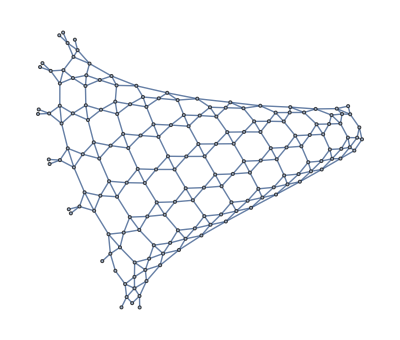

```mathematica
GraphPlot[FromNetDifferenceSets[%199]]
```

```mathematica
{IC[
IC[IC[{1,2},2],{3+3 k,4+3 k},k],                                           {5+3 k,6+3 k},{1,2,3},{6+3 k,7+3 k},{1,2},{4+3 k,6+3 k},IC[IC[{1,2},2],{5+3 k,6+3 k},k],{1,2},{1,9+3 k},{5+3 k,6+3 k},{1,2,3},{7+3 k,8+3 k},{1,2},{5+3 k,7+3 k},

{k,0,5}
]}/.IC->IndexedConcatenate
```

```mathematica
{IC[
IC[IC[{1,2},2],{3+3 k,4+3 k},k],                                           {5+3 k,6+3 k},{1,2,3},{6+3 k,7+3 k},{1,2},{4+3 k,6+3 k},IC[IC[{1,2},2],{5+3 k,6+3 k},k],{1,2},{1,9+3 k},{5+3 k,6+3 k},{1,2,3},{7+3 k,8+3 k},{1,2},{5+3 k,7+3 k},

{k,0,5}
]}/.IC->IndexedConcatenate
```

```mathematica
{IC[
IC[
IC[IC[{1,2},2],{3+2m+3 k,4+2m+3 k},k], IC[{1,2},{1,9+3k},m],{5+3 k,6+3 k},
{1,2,3},{6+m+3 k,7+m+3 k},
{1,2},{4+m+3 k,6+m+3 k},
{m,0,1}],
{k,0,5}
]}/.IC->IndexedConcatenate
```

{€_(k⊨0)^5[€_(m⊨0)^1[€^k[€^2[{1,2}],{3+3 k+2 m,4+3 k+2 m}],€^m[{1,2},{1,9+3 k}],{5+3 k,6+3 k},{1,2,3},{6+3 k+m,7+3 k+m},{1,2},{4+3 k+m,6+3 k+m}]]}

="="€_(n⊨0)^3{€_(i⊨0)^(3-n){3-i-n}}{{3,2,1,0},{2,1,0},{1,0},{0}}

```mathematica
{IC[{IC[i,{i,1,3-n}]},{IC[6+i+3 k+m-2 n+i n,{i,0,1}]},{n,0,1}]}/.IC->IndexedConcatenate
```

{€_(n⊨0)^1[{€_(i⊨1)^(3-n)[i]},{€_(i⊨0)^1[6+i+3 k+m-2 n+i n]}]}

```mathematica
ExpandAll[%]
```

{{1,2,3},{6+3 k+m,7+3 k+m},{1,2},{4+3 k+m,6+3 k+m}}

```mathematica
{IC[
IC[
IC[IC[{1,2},2],{3+2m+3 k,4+2m+3 k},k], IC[{1,2},{1,9+3k},m],{5+3 k,6+3 k},
IC[{IC[i,{i,1,3-n}]},{IC[6+i+3 k+m-2 n+i n,{i,0,1}]},{n,0,1}],
{m,0,1}],
{k,0,6}
]}/.IC->IndexedConcatenate
```

{€_(k⊨0)^6[€_(m⊨0)^1[€^k[€^2[{1,2}],{3 k+2 m+3,3 k+2 m+4}],€^m[{1,2},{1,3 k+9}],{3 k+5,3 k+6},€_(n⊨0)^1[{€_(i⊨1)^(3-n)[i]},{€_(i⊨0)^1[n i+i+3 k+m-2 n+6]}]]]}

```mathematica
%//ExpandAll
```

{{5,6},{1,2,3},{6,7},{1,2},{4,6},{1,2},{1,9},{5,6},{1,2,3},{7,8},{1,2},{5,7},{1,2},{1,2},{6,7},{8,9},{1,2,3},{9,10},{1,2},{7,9},{1,2},{1,2},{8,9},{1,2},{1,12},{8,9},{1,2,3},{10,11},{1,2},{8,10},{1,2},{1,2},{9,10},{1,2},{1,2},{9,10},{11,12},{1,2,3},{12,13},{1,2},{10,12},{1,2},{1,2},{11,12},{1,2},{1,2},{11,12},{1,2},{1,15},{11,12},{1,2,3},{13,14},{1,2},{11,13},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{14,15},{1,2,3},{15,16},{1,2},{13,15},{1,2},{1,2},{14,15},{1,2},{1,2},{14,15},{1,2},{1,2},{14,15},{1,2},{1,18},{14,15},{1,2,3},{16,17},{1,2},{14,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{17,18},{1,2,3},{18,19},{1,2},{16,18},{1,2},{1,2},{17,18},{1,2},{1,2},{17,18},{1,2},{1,2},{17,18},{1,2},{1,2},{17,18},{1,2},{1,21},{17,18},{1,2,3},{19,20},{1,2},{17,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{20,21},{1,2,3},{21,22},{1,2},{19,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,24},{20,21},{1,2,3},{22,23},{1,2},{20,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{23,24},{1,2,3},{24,25},{1,2},{22,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,27},{23,24},{1,2,3},{25,26},{1,2},{23,25}}

```mathematica
Length[%199]
```

162

```mathematica
Length[%257]
```

210

```mathematica
%199[[1;;162]]==%257[[1;;162]]
```

True

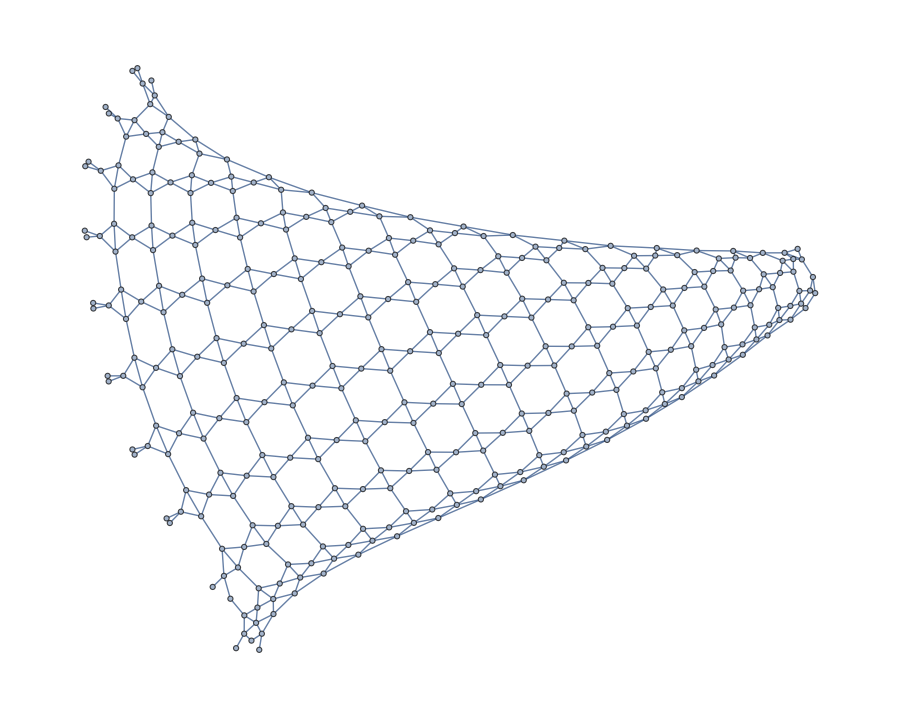

```mathematica
{IC[
IC[
IC[IC[{1,2},2],{3+2m+3 k,4+2m+3 k},k], IC[{1,2},{1,9+3k},m],{5+3 k,6+3 k},
IC[{IC[i,{i,1,3-n}]},{IC[6+i+3 k+m-2 n+i n,{i,0,1}]},{n,0,1}],
{m,0,1}],
{k,0,8}
]}/.IC->IndexedConcatenate//ExpandAll//FromNetDifferenceSets//GraphPlot
```

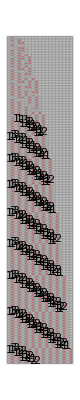
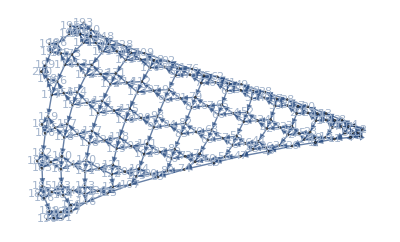
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSSDisplay[sss01]
```

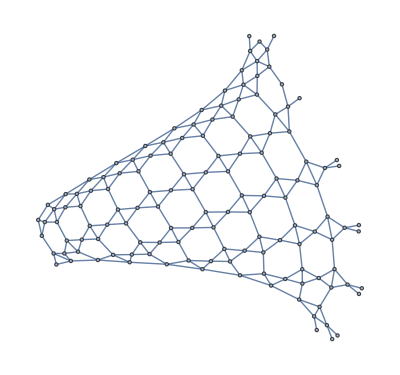

```mathematica
{IC[
IC[
IC[IC[{1,2},2],{3+2m+3 k,4+2m+3 k},k], IC[{1,2},{1,9+3k},m],{5+3 k,6+3 k},
IC[{IC[i,{i,1,3-n}]},{IC[6+i+3 k+m-2 n+i n,{i,0,1}]},{n,0,1}],
{m,0,1}],
{k,0,4}
]}/.IC->IndexedConcatenate//ExpandAll//FromNetDifferenceSets//GraphPlot
```

```mathematica
{IC[
IC[
IC[IC[{1,2},2],{3+2m+3 k,4+2m+3 k},k], IC[{1,2},{1,9+3k},m],{5+3 k,6+3 k},
IC[{IC[i,{i,1,3-n}]},{IC[6+i+3 k+m-2 n+i n,{i,0,1}]},{n,0,1}],
{m,0,1}],
{k,0,4}
]}/.IC->IndexedConcatenate
```

{€_(k⊨0)^4[€_(m⊨0)^1[€^k[€^2[{1,2}],{3 k+2 m+3,3 k+2 m+4}],€^m[{1,2},{1,3 k+9}],{3 k+5,3 k+6},€_(n⊨0)^1[{€_(i⊨1)^(3-n)[i]},{€_(i⊨0)^1[n i+i+3 k+m-2 n+6]}]]]}

```mathematica
{IC[
IC[
IC[IC[{IC[i,{i,1,2}]},2],{IC[3+n+2m+3 k,{n,0,1}]},k], IC[{IC[i,{i,1,2}]},{1,9+3k},m],{IC[i+5+3 k,{i,0,1}]},
IC[{IC[i,{i,1,3-n}]},{IC[6+i+3 k+m-2 n+i n,{i,0,1}]},{n,0,1}],
{m,0,1}],
{k,0,4}
]}/.IC->IndexedConcatenate
```

{€_(k⊨0)^4[€_(m⊨0)^1[€^k[€^2[{€_(i⊨1)^2[i]}],{€_(n⊨0)^1[3+3 k+2 m+n]}],€^m[{€_(i⊨1)^2[i]},{1,9+3 k}],{€_(i⊨0)^1[5+i+3 k]},€_(n⊨0)^1[{€_(i⊨1)^(3-n)[i]},{€_(i⊨0)^1[6+i+3 k+m-2 n+i n]}]]]}

```mathematica
{IC[
IC[
IC[IC[{IC[i,{i,1,2}]},2],{IC[3+n+2m+3 k,{n,0,1}]},k], IC[{IC[i,{i,1,2}]},{1,9+3k},m],{IC[i+5+3 k,{i,0,1}]},
IC[{IC[i,{i,1,3-n}]},{IC[6+i+3 k+m-2 n+i n,{i,0,1}]},{n,0,1}],
{m,0,1}],
{k,0,4}
]}/.IC->IndexedConcatenate//ExpandAll//FromNetDifferenceSets//GraphPlot
```

-Graphics-

## Trying again

```mathematica
nds01
```

```mathematica
{{1,2,4},{1,2},{1,2,3},{3,4},{1,6},{1,3},{1,2,3},{4,5},{1,2},{2,4},{5,6},{1,2,3},{6,7},{1,2},{4,6},{1,2},{1,9},{5,6},{1,2,3},{7,8},{1,2},{5,7},IC[{1,2},2],{6,7},{8,9},{1,2,3},{9,10},{1,2},{7,9},IC[{1,2},2],{8,9},{1,2},{1,12},{8,9},{1,2,3},{10,11},{1,2},{8,10},IC[{1,2},2],{9,10},IC[{1,2},2],{9,10},{11,12},{1,2,3},{12,13},{1,2},{10,12},IC[{1,2},2],{11,12},IC[{1,2},2],{11,12},{1,2},{1,15},{11,12},{1,2,3},{13,14},{1,2},{11,13},IC[{1,2},2],{12,13},IC[{1,2},2],{12,13},IC[{1,2},2],{12,13},{14,15},{1,2,3},{15,16},{1,2},{13,15},IC[{1,2},2],{14,15},IC[{1,2},2],{14,15},IC[{1,2},2],{14,15},{1,2},{1,18},{14,15},{1,2,3},{16,17},{1,2},{14,16},IC[{1,2},2],{15,16},IC[{1,2},2],{15,16},IC[{1,2},2],{15,16},IC[{1,2},2],{15,16},{17,18},{1,2,3},{18,19},{1,2},{16,18},IC[{1,2},2],{17,18},IC[{1,2},2],{17,18},IC[{1,2},2],{17,18},IC[{1,2},2],{17,18},{1,2},{1,21},{17,18},{1,2,3},{19,20},{1,2},{17,19},IC[{1,2},2],{18,19},IC[{1,2},2],{18,19},IC[{1,2},2],{18,19},IC[{1,2},2],{18,19},IC[{1,2},2],{18,19},{20,21},{1,2,3},{21,22},{1,2},{19,21},IC[{1,2},2],{20,21},IC[{1,2},2],{20,21},IC[{1,2},2],{20,21},IC[{1,2},2],{20,21},IC[{1,2},2],{20,21},{1,2},{1,24},{20,21},{1,2,3},{22,23},{1,2},{20,22},IC[{1,2},2],{21,22},IC[{1,2},2],{21,22},IC[{1,2},2],{21,22},IC[{1,2},2],{21,22},IC[{1,2},2],{21,22},IC[{1,2},2],{21,22},{23,24},{1,2,3},{24,25},{1,2},{22,24},IC[{1,2},2],{23,24},IC[{1,2},2],{23,24},IC[{1,2},2],{23,24},IC[{1,2},2],{23,24},IC[{1,2},2],{23,24},IC[{1,2},2],{23,24},{1,2},{1,27},{23,24},{1,2,3},{25,26},{1,2},{23,25},IC[{1,2},2],{24,25},IC[{1,2},2],{24,25},IC[{1,2},2],{24,25},IC[{1,2},2],{24,25},IC[{1,2},2],{24,25},IC[{1,2},2],{24,25},IC[{1,2},2],{24,25},{26,27},{1,2,3},{27,28},{1,2},{25,27},IC[{1,2},2],{26,27},IC[{1,2},2],{26,27},IC[{1,2},2],{26,27},IC[{1,2},2],{26,27},IC[{1,2},2],{26,27},IC[{1,2},2],{26,27},IC[{1,2},2],{26,27},{1,2},{1,30},{26,27},{1,2,3},{28,29},{1,2},{26,28},IC[{1,2},2],{27,28},IC[{1,2},2],{27,28},IC[{1,2},2],{27,28},IC[{1,2},2],{27,28},IC[{1,2},2],{27,28},IC[{1,2},2],{27,28},IC[{1,2},2],{27,28},IC[{1,2},2],{27,28},{29,30},{1,2,3},{30,31},{1,2},{28,30},IC[{1,2},2],{29,30},IC[{1,2},2],{29,30},IC[{1,2},2],{29,30},IC[{1,2},2],{29,30},IC[{1,2},2],{29,30},IC[{1,2},2],{29,30},IC[{1,2},2],{29,30},IC[{1,2},2],{29,30},{1,2},{1,33},{29,30},{1,2,3},{31,32},{1,2},{29,31},IC[{1,2},2],{30,31},IC[{1,2},2],{30,31},IC[{1,2},2],{30,31},IC[{1,2},2],{30,31},IC[{1,2},2],{30,31},IC[{1,2},2],{30,31},IC[{1,2},2],{30,31},IC[{1,2},2],{30,31},IC[{1,2},2],{30,31},{32,33},{1,2,3},{33,34},{1,2},{31,33},IC[{1,2},2],{32,33},IC[{1,2},2],{32,33},IC[{1,2},2],{32,33},IC[{1,2},2],{32,33},IC[{1,2},2],{32,33},IC[{1,2},2],{32,33},IC[{1,2},2],{32,33},IC[{1,2},2],{32,33},IC[{1,2},2],{32,33},{1,2},{1,36},{32,33},{1,2,3},{34,35},{1,2},{32,34},IC[{1,2},2],{33,34},IC[{1,2},2],{33,34},IC[{1,2},2],{33,34},IC[{1,2},2],{33,34},IC[{1,2},2],{33,34},IC[{1,2},2],{33,34},IC[{1,2},2],{33,34},IC[{1,2},2],{33,34},IC[{1,2},2],{33,34},IC[{1,2},2],{33,34},{35,36},{1,2,3},{36,37},{1,2},{34,36},IC[{1,2},2],{35,36},IC[{1,2},2],{35,36},IC[{1,2},2],{35,36},IC[{1,2},2],{35,36},IC[{1,2},2],{35,36},IC[{1,2},2],{35,36},IC[{1,2},2],{35,36},IC[{1,2},2],{35,36},IC[{1,2},2],{35,36},IC[{1,2},2],{35,36},{1,2},{1,39},{35,36},{1,2,3},{37,38},{1,2},{35,37},IC[{1,2},2],{36,37},IC[{1,2},2],{36,37},IC[{1,2},2],{36,37},IC[{1,2},2],{36,37},IC[{1,2},2],{36,37},IC[{1,2},2],{36,37},IC[{1,2},2],{36,37},IC[{1,2},2],{36,37},IC[{1,2},2],{36,37},IC[{1,2},2],{36,37},IC[{1,2},2],{36,37},{38,39},{1,2,3},{39,40},{1,2},{37,39},IC[{1,2},2],{38,39},IC[{1,2},2],{38,39},IC[{1,2},2],{38,39},IC[{1,2},2],{38,39},IC[{1,2},2],{38,39},IC[{1,2},2],{38,39},IC[{1,2},2],{38,39},IC[{1,2},2],{38,39},IC[{1,2},2],{38,39},IC[{1,2},2],{38,39},IC[{1,2},2],{38,39},{1,2},{1,42},{38,39},{1,2,3},{40,41},{1,2},{38,40},IC[{1,2},2],{39,40},IC[{1,2},2],{39,40},IC[{1,2},2],{39,40},IC[{1,2},2],{39,40},IC[{1,2},2],{39,40},IC[{1,2},2],{39,40},IC[{1,2},2],{39,40},IC[{1,2},2],{39,40},IC[{1,2},2],{39,40},IC[{1,2},2],{39,40},IC[{1,2},2],{39,40},IC[{1,2},2],{39,40},{41,42},{1,2,3},{42,43},{1,2},{40,42},IC[{1,2},2],{41,42},IC[{1,2},2],{41,42},IC[{1,2},2],{41,42},IC[{1,2},2],{41,42},IC[{1,2},2],{41,42},IC[{1,2},2],{41,42},IC[{1,2},2],{41,42},IC[{1,2},2],{41,42},IC[{1,2},2],{41,42},IC[{1,2},2],{41,42},IC[{1,2},2],{41,42},IC[{1,2},2],{41,42},{1,2},{1,45},{41,42},{1,2,3},{43,44},{1,2},{41,43},IC[{1,2},2],{42,43},IC[{1,2},2],{42,43},IC[{1,2},2],{42,43},IC[{1,2},2],{42,43},IC[{1,2},2],{42,43},IC[{1,2},2],{42,43},IC[{1,2},2],{42,43},IC[{1,2},2],{42,43},IC[{1,2},2],{42,43},IC[{1,2},2],{42,43},IC[{1,2},2],{42,43},IC[{1,2},2],{42,43},IC[{1,2},2],{42,43},{44,45},{1,2,3},{45,46},{1,2},{43,45},IC[{1,2},2],{44,45},IC[{1,2},2],{44,45},IC[{1,2},2],{44,45},IC[{1,2},2],{44,45},IC[{1,2},2],{44,45},IC[{1,2},2],{44,45},IC[{1,2},2],{44,45},IC[{1,2},2],{44,45},IC[{1,2},2],{44,45},IC[{1,2},2],{44,45},IC[{1,2},2],{44,45},IC[{1,2},2],{44,45},IC[{1,2},2],{44,45},{1,2},{1,48},{44,45},{1,2,3},{46,47},{1,2},{44,46},IC[{1,2},2],{45,46},IC[{1,2},2],{45,46},IC[{1,2},2],{45,46},IC[{1,2},2],{45,46},IC[{1,2},2],{45,46},IC[{1,2},2],{45,46},IC[{1,2},2],{45,46},IC[{1,2},2],{45,46},IC[{1,2},2],{45,46},IC[{1,2},2],{45,46},IC[{1,2},2],{45,46},IC[{1,2},2],{45,46},IC[{1,2},2],{45,46},IC[{1,2},2],{45,46},{47,48},{1,2,3},{48,49},{1,2},{46,48},IC[{1,2},2],{47,48},IC[{1,2},2],{47,48},IC[{1,2},2],{47,48},IC[{1,2},2],{47,48},IC[{1,2},2],{47,48},IC[{1,2},2],{47,48},IC[{1,2},2],{47,48},IC[{1,2},2],{47,48},IC[{1,2},2],{47,48},IC[{1,2},2],{47,48},IC[{1,2},2],{47,48},IC[{1,2},2],{47,48},IC[{1,2},2],{47,48},IC[{1,2},2],{47,48},{1,2},{1,51},{47,48},{1,2,3},{49,50},{1,2},{47,49},IC[{1,2},2],{48,49},IC[{1,2},2],{48,49},IC[{1,2},2],{48,49},IC[{1,2},2],{48,49},IC[{1,2},2],{48,49},IC[{1,2},2],{48,49},IC[{1,2},2],{48,49},IC[{1,2},2],{48,49},IC[{1,2},2],{48,49},IC[{1,2},2],{48,49},IC[{1,2},2],{48,49},IC[{1,2},2],{48,49},IC[{1,2},2],{48,49},IC[{1,2},2],{48,49},IC[{1,2},2],{48,49},{50,51},{1,2,3},{51,52},{1,2},{49,51},IC[{1,2},2],{50,51},IC[{1,2},2],{50,51},IC[{1,2},2],{50,51},IC[{1,2},2],{50,51},IC[{1,2},2],{50,51},IC[{1,2},2],{50,51},IC[{1,2},2],{50,51},IC[{1,2},2],{50,51},IC[{1,2},2],{50,51},IC[{1,2},2],{50,51},IC[{1,2},2],{50,51},IC[{1,2},2],{50,51},IC[{1,2},2],{50,51},IC[{1,2},2],{50,51},IC[{1,2},2],{50,51},{1,2},{1,54},{50,51},{1,2,3},{52,53},{1,2},{50,52},IC[{1,2},2],{51,52},IC[{1,2},2],{51,52},IC[{1,2},2],{51,52},IC[{1,2},2],{51,52},IC[{1,2},2],{51,52},IC[{1,2},2],{51,52},IC[{1,2},2],{51,52},IC[{1,2},2],{51,52},IC[{1,2},2],{51,52},IC[{1,2},2],{51,52},IC[{1,2},2],{51,52},IC[{1,2},2],{51,52},IC[{1,2},2],{51,52},IC[{1,2},2],{51,52},IC[{1,2},2],{51,52},IC[{1,2},2],{51,52},{53,54},{1,2,3},{54,55},{1,2},{52,54},IC[{1,2},2],{53,54},IC[{1,2},2],{53,54},IC[{1,2},2],{53,54},IC[{1,2},2],{53,54},IC[{1,2},2],{53,54},IC[{1,2},2],{53,54},IC[{1,2},2],{53,54},IC[{1,2},2],{53,54},IC[{1,2},2],{53,54},IC[{1,2},2],{53,54},IC[{1,2},2],{53,54},IC[{1,2},2],{53,54},IC[{1,2},2],{53,54},IC[{1,2},2],{53,54},IC[{1,2},2],{53,54},IC[{1,2},2],{53,54},{1,2},{1,57},{53,54},{1,2,3},{55,56},{1,2},{53,55},IC[{1,2},2],{54,55},IC[{1,2},2],{54,55},IC[{1,2},2],{54,55},IC[{1,2},2],{54,55},IC[{1,2},2],{54,55},IC[{1,2},2],{54,55},IC[{1,2},2],{54,55},IC[{1,2},2],{54,55},IC[{1,2},2],{54,55},IC[{1,2},2],{54,55},IC[{1,2},2],{54,55},IC[{1,2},2],{54,55},IC[{1,2},2],{54,55},IC[{1,2},2],{54,55},IC[{1,2},2],{54,55},IC[{1,2},2],{54,55},IC[{1,2},2],{54,55},{56,57},{1,2,3},{57,58},{1,2},{55,57},IC[{1,2},2],{56,57},IC[{1,2},2],{56,57},IC[{1,2},2],{56,57},IC[{1,2},2],{56,57},IC[{1,2},2],{56,57},IC[{1,2},2],{56,57},IC[{1,2},2],{56,57},IC[{1,2},2],{56,57},IC[{1,2},2],{56,57},IC[{1,2},2],{56,57},IC[{1,2},2],{56,57},IC[{1,2},2],{56,57},IC[{1,2},2],{56,57},IC[{1,2},2],{56,57},IC[{1,2},2],{56,57},IC[{1,2},2],{56,57},IC[{1,2},2],{56,57},{1,2},{1,60},{56,57},{1,2,3},{58,59},{1,2},{56,58},IC[{1,2},2],{57,58},IC[{1,2},2],{57,58},IC[{1,2},2],{57,58},IC[{1,2},2],{57,58},IC[{1,2},2],{57,58},IC[{1,2},2],{57,58},IC[{1,2},2],{57,58},IC[{1,2},2],{57,58},IC[{1,2},2],{57,58},IC[{1,2},2],{57,58},IC[{1,2},2],{57,58},IC[{1,2},2],{57,58},IC[{1,2},2],{57,58},IC[{1,2},2],{57,58},IC[{1,2},2],{57,58},IC[{1,2},2],{57,58},IC[{1,2},2],{57,58},IC[{1,2},2],{57,58},{59,60},{1,2,3},{60,61},{1,2},{58,60},IC[{1,2},2],{59,60},IC[{1,2},2],{59,60},IC[{1,2},2],{59,60},IC[{1,2},2],{59,60},IC[{1,2},2],{59,60},IC[{1,2},2],{59,60},IC[{1,2},2],{59,60},IC[{1,2},2],{59,60},IC[{1,2},2],{59,60},IC[{1,2},2],{59,60},IC[{1,2},2],{59,60},IC[{1,2},2],{59,60},IC[{1,2},2],{59,60},IC[{1,2},2],{59,60},IC[{1,2},2],{59,60},IC[{1,2},2],{59,60},IC[{1,2},2],{59,60},IC[{1,2},2],{59,60},{1,2},{1,63},{59,60},{1,2,3},{61,62},{1,2},{59,61},IC[{1,2},2],{60,61},IC[{1,2},2],{60,61},IC[{1,2},2],{60,61},IC[{1,2},2],{60,61},IC[{1,2},2],{60,61},IC[{1,2},2],{60,61},IC[{1,2},2],{60,61},IC[{1,2},2],{60,61},IC[{1,2},2],{60,61},IC[{1,2},2],{60,61},IC[{1,2},2],{60,61},IC[{1,2},2],{60,61},IC[{1,2},2],{60,61},IC[{1,2},2],{60,61},IC[{1,2},2],{60,61},IC[{1,2},2],{60,61},IC[{1,2},2],{60,61},IC[{1,2},2],{60,61},IC[{1,2},2],{60,61},{62,63},{1,2,3},{63,64},{1,2},{61,63},IC[{1,2},2],{62,63},IC[{1,2},2],{62,63},IC[{1,2},2],{62,63},IC[{1,2},2],{62,63},IC[{1,2},2],{62,63},IC[{1,2},2],{62,63},IC[{1,2},2],{62,63},IC[{1,2},2],{62,63},IC[{1,2},2],{62,63},IC[{1,2},2],{62,63},IC[{1,2},2],{62,63},IC[{1,2},2],{62,63},IC[{1,2},2],{62,63},IC[{1,2},2],{62,63},IC[{1,2},2],{62,63},IC[{1,2},2],{62,63},IC[{1,2},2],{62,63},IC[{1,2},2],{62,63},IC[{1,2},2],{62,63},{1,2},{1,66},{62,63},{1,2,3},{64,65},{1,2},{62,64},IC[{1,2},2],{63,64},IC[{1,2},2],{63,64},IC[{1,2},2],{63,64},IC[{1,2},2],{63,64},IC[{1,2},2],{63,64},IC[{1,2},2],{63,64},IC[{1,2},2],{63,64},IC[{1,2},2],{63,64},IC[{1,2},2],{63,64},IC[{1,2},2],{63,64},IC[{1,2},2],{63,64},IC[{1,2},2],{63,64},IC[{1,2},2],{63,64},IC[{1,2},2],{63,64},IC[{1,2},2],{63,64},IC[{1,2},2],{63,64},IC[{1,2},2],{63,64},IC[{1,2},2],{63,64},IC[{1,2},2],{63,64},IC[{1,2},2],{63,64},{65,66},{1,2,3},{66,67},{1,2},{64,66},IC[{1,2},2],{65,66},IC[{1,2},2],{65,66},IC[{1,2},2],{65,66},IC[{1,2},2],{65,66},IC[{1,2},2],{65,66},IC[{1,2},2],{65,66},IC[{1,2},2],{65,66},IC[{1,2},2],{65,66},IC[{1,2},2],{65,66},IC[{1,2},2],{65,66},IC[{1,2},2],{65,66},IC[{1,2},2],{65,66},IC[{1,2},2],{65,66},IC[{1,2},2],{65,66},IC[{1,2},2],{65,66},IC[{1,2},2],{65,66},IC[{1,2},2],{65,66},IC[{1,2},2],{65,66},IC[{1,2},2],{65,66},IC[{1,2},2],{65,66},{1,2},{1,69},{65,66},{1,2,3},{67,68},{1,2},{65,67},IC[{1,2},2],{66,67},IC[{1,2},2],{66,67},IC[{1,2},2],{66,67},IC[{1,2},2],{66,67},IC[{1,2},2],{66,67},IC[{1,2},2],{66,67},IC[{1,2},2],{66,67},IC[{1,2},2],{66,67},IC[{1,2},2],{66,67},IC[{1,2},2],{66,67},IC[{1,2},2],{66,67},IC[{1,2},2],{66,67},IC[{1,2},2],{66,67},IC[{1,2},2],{66,67},IC[{1,2},2],{66,67},IC[{1,2},2],{66,67},IC[{1,2},2],{66,67},IC[{1,2},2],{66,67},IC[{1,2},2],{66,67},IC[{1,2},2],{66,67},IC[{1,2},2],{66,67},{68,69},{1,2,3},{69,70},{1,2},{67,69},IC[{1,2},2],{68,69},IC[{1,2},2],{68,69},IC[{1,2},2],{68,69},IC[{1,2},2],{68,69},IC[{1,2},2],{68,69},IC[{1,2},2],{68,69},IC[{1,2},2],{68,69},IC[{1,2},2],{68,69},IC[{1,2},2],{68,69},IC[{1,2},2],{68,69},IC[{1,2},2],{68,69},IC[{1,2},2],{68,69},IC[{1,2},2],{68,69},IC[{1,2},2],{68,69},IC[{1,2},2],{68,69},IC[{1,2},2],{68,69},IC[{1,2},2],{68,69},IC[{1,2},2],{68,69},IC[{1,2},2],{68,69},IC[{1,2},2],{68,69},IC[{1,2},2],{68,69},{1,2},{1,72},{68,69},{1,2,3},{70,71},{1,2},{68,70},IC[{1,2},2],{69,70},IC[{1,2},2],{69,70},IC[{1,2},2],{69,70},IC[{1,2},2],{69,70},IC[{1,2},2],{69,70},IC[{1,2},2],{69,70},IC[{1,2},2],{69,70},IC[{1,2},2],{69,70},IC[{1,2},2],{69,70},IC[{1,2},2],{69,70},IC[{1,2},2],{69,70},IC[{1,2},2],{69,70},IC[{1,2},2],{69,70},IC[{1,2},2],{69,70},IC[{1,2},2],{69,70},IC[{1,2},2],{69,70},IC[{1,2},2],{69,70},IC[{1,2},2],{69,70},IC[{1,2},2],{69,70},IC[{1,2},2],{69,70},IC[{1,2},2],{69,70},IC[{1,2},2],{69,70},{71,72},{1,2,3},{72,73},{1,2},{70,72},IC[{1,2},2],{71,72},IC[{1,2},2],{71,72},IC[{1,2},2],{71,72},IC[{1,2},2],{71,72},IC[{1,2},2],{71,72},IC[{1,2},2],{71,72},IC[{1,2},2],{71,72},IC[{1,2},2],{71,72},IC[{1,2},2],{71,72},IC[{1,2},2],{71,72},IC[{1,2},2],{71,72},IC[{1,2},2],{71,72},IC[{1,2},2],{71,72},IC[{1,2},2],{71,72},IC[{1,2},2],{71,72},IC[{1,2},2],{71,72},IC[{1,2},2],{71,72},IC[{1,2},2],{71,72},IC[{1,2},2],{71,72},IC[{1,2},2],{71,72},IC[{1,2},2],{71,72},IC[{1,2},2],{71,72},{1,2},{1,75},{71,72},{1,2,3},{73,74},{1,2},{71,73},IC[{1,2},2],{72,73},IC[{1,2},2],{72,73},IC[{1,2},2],{72,73},IC[{1,2},2],{72,73},IC[{1,2},2],{72,73},IC[{1,2},2],{72,73},IC[{1,2},2],{72,73},IC[{1,2},2],{72,73},IC[{1,2},2],{72,73},IC[{1,2},2],{72,73},IC[{1,2},2],{72,73},IC[{1,2},2],{72,73},IC[{1,2},2],{72,73},IC[{1,2},2],{72,73},IC[{1,2},2],{72,73},IC[{1,2},2],{72,73},IC[{1,2},2],{72,73},IC[{1,2},2],{72,73},IC[{1,2},2],{72,73},IC[{1,2},2],{72,73},IC[{1,2},2],{72,73},IC[{1,2},2],{72,73},IC[{1,2},2],{72,73},{74,75},{1,2,3},{75,76},{1,2},{73,75},IC[{1,2},2],{74,75},IC[{1,2},2],{74,75},IC[{1,2},2],{74,75},IC[{1,2},2],{74,75},IC[{1,2},2],{74,75},IC[{1,2},2],{74,75},IC[{1,2},2],{74,75},IC[{1,2},2],{74,75},IC[{1,2},2],{74,75},IC[{1,2},2],{74,75},IC[{1,2},2],{74,75},IC[{1,2},2],{74,75},IC[{1,2},2],{74,75},IC[{1,2},2],{74,75},IC[{1,2},2],{74,75},IC[{1,2},2],{74,75},IC[{1,2},2],{74,75},IC[{1,2},2],{74,75},IC[{1,2},2],{74,75},IC[{1,2},2],{74,75},IC[{1,2},2],{74,75},IC[{1,2},2],{74,75},IC[{1,2},2],{74,75},{1,2},{1,78},{74,75},{1,2,3},{76,77},{1,2},{74,76},IC[{1,2},2],{75,76},IC[{1,2},2],{75,76},IC[{1,2},2],{75,76},IC[{1,2},2],{75,76},IC[{1,2},2],{75,76},IC[{1,2},2],{75,76},IC[{1,2},2],{75,76},IC[{1,2},2],{75,76},IC[{1,2},2],{75,76},IC[{1,2},2],{75,76},IC[{1,2},2],{75,76},IC[{1,2},2],{75,76},IC[{1,2},2],{75,76},IC[{1,2},2],{75,76},IC[{1,2},2],{75,76},IC[{1,2},2],{75,76},IC[{1,2},2],{75,76},IC[{1,2},2],{75,76},IC[{1,2},2],{75,76},IC[{1,2},2],{75,76},IC[{1,2},2],{75,76},IC[{1,2},2],{75,76},IC[{1,2},2],{75,76},IC[{1,2},2],{75,76},{77,78},{1,2,3},{78,79},{1,2},{76,78},IC[{1,2},2],{77,78},IC[{1,2},2],{77,78},IC[{1,2},2],{77,78},IC[{1,2},2],{77,78},IC[{1,2},2],{77,78},IC[{1,2},2],{77,78},IC[{1,2},2],{77,78},IC[{1,2},2],{77,78},IC[{1,2},2],{77,78},IC[{1,2},2],{77,78},IC[{1,2},2],{77,78},IC[{1,2},2],{77,78},IC[{1,2},2],{77,78},IC[{1,2},2],{77,78},IC[{1,2},2],{77,78},IC[{1,2},2],{77,78},IC[{1,2},2],{77,78},IC[{1,2},2],{77,78},IC[{1,2},2],{77,78},IC[{1,2},2],{77,78},IC[{1,2},2],{77,78},IC[{1,2},2],{77,78},IC[{1,2},2],{77,78},IC[{1,2},2],{77,78},{1,2},{1,81},{77,78},{1,2,3},{79,80},{1,2},{77,79},IC[{1,2},2],{78,79},IC[{1,2},2],{78,79},IC[{1,2},2],{78,79},IC[{1,2},2],{78,79},IC[{1,2},2],{78,79},IC[{1,2},2],{78,79},IC[{1,2},2],{78,79},IC[{1,2},2],{78,79},IC[{1,2},2],{78,79},IC[{1,2},2],{78,79},IC[{1,2},2],{78,79},IC[{1,2},2],{78,79},IC[{1,2},2],{78,79},IC[{1,2},2],{78,79},IC[{1,2},2],{78,79},IC[{1,2},2],{78,79},IC[{1,2},2],{78,79},IC[{1,2},2],{78,79},IC[{1,2},2],{78,79},IC[{1,2},2],{78,79},IC[{1,2},2],{78,79},IC[{1,2},2],{78,79},IC[{1,2},2],{78,79},IC[{1,2},2],{78,79},IC[{1,2},2],{78,79},{80,81},{1,2,3},{81,82},{1,2},{79,81},IC[{1,2},2],{80,81},IC[{1,2},2],{80,81},IC[{1,2},2],{80,81},IC[{1,2},2],{80,81},IC[{1,2},2],{80,81},IC[{1,2},2],{80,81},IC[{1,2},2],{80,81},IC[{1,2},2],{80,81},IC[{1,2},2],{80,81},IC[{1,2},2],{80,81},IC[{1,2},2],{80,81},IC[{1,2},2],{80,81},IC[{1,2},2],{80,81},IC[{1,2},2],{80,81},IC[{1,2},2],{80,81},IC[{1,2},2],{80,81},IC[{1,2},2],{80,81},IC[{1,2},2],{80,81},IC[{1,2},2],{80,81},IC[{1,2},2],{80,81},IC[{1,2},2],{80,81},IC[{1,2},2],{80,81},IC[{1,2},2],{80,81},IC[{1,2},2],{80,81},IC[{1,2},2],{80,81},{1,2},{1,84},{80,81},{1,2,3},{82,83},{1,2},{80,82},IC[{1,2},2],{81,82},IC[{1,2},2],{81,82},IC[{1,2},2],{81,82},IC[{1,2},2],{81,82},IC[{1,2},2],{81,82},IC[{1,2},2],{81,82},IC[{1,2},2],{81,82},IC[{1,2},2],{81,82},IC[{1,2},2],{81,82},IC[{1,2},2],{81,82},IC[{1,2},2],{81,82},IC[{1,2},2],{81,82},IC[{1,2},2],{81,82},IC[{1,2},2],{81,82},IC[{1,2},2],{81,82},IC[{1,2},2],{81,82},IC[{1,2},2],{81,82},IC[{1,2},2],{81,82},IC[{1,2},2],{81,82},IC[{1,2},2],{81,82},IC[{1,2},2],{81,82},IC[{1,2},2],{81,82},IC[{1,2},2],{81,82},IC[{1,2},2],{81,82},IC[{1,2},2],{81,82},IC[{1,2},2],{81,82},{83,84},{1,2,3},{84,85},{1,2},{82,84},IC[{1,2},2],{83,84},IC[{1,2},2],{83,84},IC[{1,2},2],{83,84},IC[{1,2},2],{83,84},IC[{1,2},2],{83,84},IC[{1,2},2],{83,84},IC[{1,2},2],{83,84},IC[{1,2},2],{83,84},IC[{1,2},2],{83,84},IC[{1,2},2],{83,84},IC[{1,2},2],{83,84},IC[{1,2},2],{83,84},IC[{1,2},2],{83,84},IC[{1,2},2],{83,84},IC[{1,2},2],{83,84},IC[{1,2},2],{83,84},IC[{1,2},2],{83,84},IC[{1,2},2],{83,84},IC[{1,2},2],{83,84},IC[{1,2},2],{83,84},IC[{1,2},2],{83,84},IC[{1,2},2],{83,84},IC[{1,2},2],{83,84},IC[{1,2},2],{83,84},IC[{1,2},2],{83,84},IC[{1,2},2],{83,84},{1,2},{1,87},{83,84},{1,2,3},{85,86},{1,2},{83,85},IC[{1,2},2],{84,85},IC[{1,2},2],{84,85},IC[{1,2},2],{84,85},IC[{1,2},2],{84,85},IC[{1,2},2],{84,85},IC[{1,2},2],{84,85},IC[{1,2},2],{84,85},IC[{1,2},2],{84,85},IC[{1,2},2],{84,85},IC[{1,2},2],{84,85},IC[{1,2},2],{84,85},IC[{1,2},2],{84,85},IC[{1,2},2],{84,85},IC[{1,2},2],{84,85},IC[{1,2},2],{84,85},IC[{1,2},2],{84,85},IC[{1,2},2],{84,85},IC[{1,2},2],{84,85},IC[{1,2},2],{84,85},IC[{1,2},2],{84,85},IC[{1,2},2],{84,85},IC[{1,2},2],{84,85},IC[{1,2},2],{84,85},IC[{1,2},2],{84,85},IC[{1,2},2],{84,85},IC[{1,2},2],{84,85},IC[{1,2},2],{84,85},{86,87},{1,2,3},{87,88},{1,2},{85,87},IC[{1,2},2],{86,87},IC[{1,2},2],{86,87},IC[{1,2},2],{86,87},IC[{1,2},2],{86,87},IC[{1,2},2],{86,87},IC[{1,2},2],{86,87},IC[{1,2},2],{86,87},IC[{1,2},2],{86,87},IC[{1,2},2],{86,87},IC[{1,2},2],{86,87},IC[{1,2},2],{86,87},IC[{1,2},2],{86,87},IC[{1,2},2],{86,87},IC[{1,2},2],{86,87},IC[{1,2},2],{86,87},IC[{1,2},2],{86,87},IC[{1,2},2],{86,87},IC[{1,2},2],{86,87},IC[{1,2},2],{86,87},IC[{1,2},2],{86,87},IC[{1,2},2],{86,87},IC[{1,2},2],{86,87},IC[{1,2},2],{86,87},IC[{1,2},2],{86,87},IC[{1,2},2],{86,87},IC[{1,2},2],{86,87},IC[{1,2},2],{86,87},{1,2},{1,90},{86,87},{1,2,3},{88,89},{1,2},{86,88},IC[{1,2},2],{87,88},IC[{1,2},2],{87,88},IC[{1,2},2],{87,88},IC[{1,2},2],{87,88},IC[{1,2},2],{87,88},IC[{1,2},2],{87,88},IC[{1,2},2],{87,88},IC[{1,2},2],{87,88},IC[{1,2},2],{87,88},IC[{1,2},2],{87,88},IC[{1,2},2],{87,88},IC[{1,2},2],{87,88},IC[{1,2},2],{87,88},IC[{1,2},2],{87,88},IC[{1,2},2],{87,88},IC[{1,2},2],{87,88},IC[{1,2},2],{87,88},IC[{1,2},2],{87,88},IC[{1,2},2],{87,88},IC[{1,2},2],{87,88},IC[{1,2},2],{87,88},IC[{1,2},2],{87,88},IC[{1,2},2],{87,88},IC[{1,2},2],{87,88},IC[{1,2},2],{87,88},IC[{1,2},2],{87,88},IC[{1,2},2],{87,88},IC[{1,2},2],{87,88},{89,90},{1,2,3},{90,91},{1,2},{88,90},IC[{1,2},2],{89,90},IC[{1,2},2],{89,90},IC[{1,2},2],{89,90},IC[{1,2},2],{89,90},IC[{1,2},2],{89,90},IC[{1,2},2],{89,90},IC[{1,2},2],{89,90},IC[{1,2},2],{89,90},IC[{1,2},2],{89,90},IC[{1,2},2],{89,90},IC[{1,2},2],{89,90},IC[{1,2},2],{89,90},IC[{1,2},2],{89,90},IC[{1,2},2],{89,90},IC[{1,2},2],{89,90},IC[{1,2},2],{89,90},IC[{1,2},2],{89,90},IC[{1,2},2],{89,90},IC[{1,2},2],{89,90},IC[{1,2},2],{89,90},IC[{1,2},2],{89,90},IC[{1,2},2],{89,90},IC[{1,2},2],{89,90},IC[{1,2},2],{89,90},IC[{1,2},2],{89,90},IC[{1,2},2],{89,90},IC[{1,2},2],{89,90},IC[{1,2},2],{89,90},{1,2},{1,93},{89,90},{1,2,3},{91,92},{1,2},{89,91},IC[{1,2},2],{90,91},IC[{1,2},2],{90,91},IC[{1,2},2],{90,91},IC[{1,2},2],{90,91},IC[{1,2},2],{90,91},IC[{1,2},2],{90,91},IC[{1,2},2],{90,91},IC[{1,2},2],{90,91},IC[{1,2},2],{90,91},IC[{1,2},2],{90,91},IC[{1,2},2],{90,91},IC[{1,2},2],{90,91},IC[{1,2},2],{90,91},IC[{1,2},2],{90,91},IC[{1,2},2],{90,91},IC[{1,2},2],{90,91},IC[{1,2},2],{90,91},IC[{1,2},2],{90,91},IC[{1,2},2],{90,91},IC[{1,2},2],{90,91},IC[{1,2},2],{90,91},IC[{1,2},2],{90,91},IC[{1,2},2],{90,91},IC[{1,2},2],{90,91},IC[{1,2},2],{90,91},IC[{1,2},2],{90,91},IC[{1,2},2],{90,91},IC[{1,2},2],{90,91},IC[{1,2},2],{90,91},{92,93},{1,2,3},{93,94},{1,2},{91,93},IC[{1,2},2],{92,93},IC[{1,2},2],{92,93},IC[{1,2},2],{92,93},IC[{1,2},2],{92,93},IC[{1,2},2],{92,93},IC[{1,2},2],{92,93},IC[{1,2},2],{92,93},IC[{1,2},2],{92,93},IC[{1,2},2],{92,93},IC[{1,2},2],{92,93},IC[{1,2},2],{92,93},IC[{1,2},2],{92,93},IC[{1,2},2],{92,93},IC[{1,2},2],{92,93},IC[{1,2},2],{92,93},IC[{1,2},2],{92,93},IC[{1,2},2],{92,93},IC[{1,2},2],{92,93},IC[{1,2},2],{92,93},IC[{1,2},2],{92,93},IC[{1,2},2],{92,93},IC[{1,2},2],{92,93},IC[{1,2},2],{92,93},IC[{1,2},2],{92,93},IC[{1,2},2],{92,93},IC[{1,2},2],{92,93},IC[{1,2},2],{92,93},IC[{1,2},2],{92,93},IC[{1,2},2],{92,93},{1,2},{1,96},{92,93},{1,2,3},{94,95},{1,2},{92,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},IC[{1,2},2],{93,94},{95,96},{1,2,3},{96,97},{1,2},{94,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},IC[{1,2},2],{95,96},{1,2},{1,99},{95,96},{1,2,3},{97,98},{1,2},{95,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},IC[{1,2},2],{96,97},{98,99},{1,2,3},{99,100},{1,2},{97,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},IC[{1,2},2],{98,99},{1,2},{1,102},{98,99},{1,2,3},{100,101},{1,2},{98,100},

IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},IC[{1,2},2],{99,100},

{101,102},{1,2,3},{102,103},{1,2},{100,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},IC[{1,2},2],{101,102},{1,2},{1,105},{101,102},{1,2,3},{103,104},{1,2},{101,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},IC[{1,2},2],{102,103},{104,105},{1,2,3},{105,106},{1,2},{103,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},IC[{1,2},2],{104,105},{1,2},{1,108},{104,105},{1,2,3},{106,107},{1,2},{104,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},IC[{1,2},2],{105,106},{107,108},{1,2,3},{108,109},{1,2}}
```

```mathematica
{{1,2,4},{1,2},{1,2,3},{3,4},{1,6},{1,3},

{1,2,3},{4,5},{1,2},{2,4},

IC[IC[{1,2},2],{3,4},0],{5,6},{1,2,3},{6,7},{1,2},{4,6},
IC[IC[{1,2},2],{5,6},0],{1,2},{1,9},{5,6},{1,2,3},{7,8},{1,2},{5,7},

IC[IC[{1,2},2],{6,7},1],{8,9},{1,2,3},{9,10},{1,2},{7,9},
IC[IC[{1,2},2],{8,9},1],{1,2},{1,12},{8,9},{1,2,3},{10,11},{1,2},{8,10},

IC[IC[{1,2},2],{9,10},2],{11,12},{1,2,3},{12,13},{1,2},{10,12},
IC[IC[{1,2},2],{11,12},2],{1,2},{1,15},{11,12},{1,2,3},{13,14},{1,2},{11,13},

IC[IC[{1,2},2],{12,13},3],{14,15},{1,2,3},{15,16},{1,2},{13,15},
IC[IC[{1,2},2],{14,15},3],{1,2},{1,18},{14,15},{1,2,3},{16,17},{1,2},{14,16},

IC[IC[{1,2},2],{15,16},4],{17,18},{1,2,3},{18,19},{1,2},{16,18},
IC[IC[{1,2},2],{17,18},4],{1,2},{1,21},{17,18},{1,2,3},{19,20},{1,2},{17,19},

IC[IC[{1,2},2],{18,19},5],{20,21},{1,2,3},{21,22},{1,2},{19,21},
IC[IC[{1,2},2],{20,21},5],{1,2},{1,24},{20,21},{1,2,3},{22,23},{1,2},{20,22},

IC[IC[{1,2},2],{21,22},6],{23,24},{1,2,3},{24,25},{1,2},{22,24},
IC[IC[{1,2},2],{23,24},6],{1,2},{1,27},{23,24},{1,2,3},{25,26},{1,2},{23,25},

IC[IC[{1,2},2],{24,25},7],{26,27},{1,2,3},{27,28},{1,2},{25,27},
IC[IC[{1,2},2],{26,27},7],{1,2},{1,30},{26,27},{1,2,3},{28,29},{1,2},{26,28},
IC[IC[{1,2},2],{27,28},8],{29,30},{1,2,3},{30,31},{1,2},{28,30},
IC[IC[{1,2},2],{29,30},8],{1,2},{1,33},{29,30},{1,2,3},{31,32},{1,2},{29,31},
IC[IC[{1,2},2],{30,31},9],{32,33},{1,2,3},{33,34},{1,2},{31,33},
IC[IC[{1,2},2],{32,33},9],{1,2},{1,36},{32,33},{1,2,3},{34,35},{1,2},{32,34},
IC[IC[{1,2},2],{33,34},10],{35,36},{1,2,3},{36,37},{1,2},{34,36},
IC[IC[{1,2},2],{35,36},10],{1,2},{1,39},{35,36},{1,2,3},{37,38},{1,2},{35,37},
IC[IC[{1,2},2],{36,37},12],{38,39},{1,2,3},{39,40},{1,2},{37,39},
IC[IC[{1,2},2],{38,39},11],{1,2},{1,42},{38,39},{1,2,3},{40,41},{1,2},{38,40},
IC[IC[{1,2},2],{39,40},12],{41,42},{1,2,3},{42,43},{1,2},{40,42},
IC[IC[{1,2},2],{41,42},12],{1,2},{1,45},{41,42},{1,2,3},{43,44},{1,2},{41,43},
IC[IC[{1,2},2],{42,43},13],{44,45},{1,2,3},{45,46},{1,2},{43,45},
IC[IC[{1,2},2],{44,45},13],{1,2},{1,48},{44,45},{1,2,3},{46,47},{1,2},{44,46},
IC[IC[{1,2},2],{45,46},14],{47,48},{1,2,3},{48,49},{1,2},{46,48},
IC[IC[{1,2},2],{47,48},14],{1,2},{1,51},{47,48},{1,2,3},{49,50},{1,2},{47,49},
IC[IC[{1,2},2],{48,49},15],{50,51},{1,2,3},{51,52},{1,2},{49,51},
IC[IC[{1,2},2],{50,51},15],{1,2},{1,54},{50,51},{1,2,3},{52,53},{1,2},{50,52},
IC[IC[{1,2},2],{51,52},16],{53,54},{1,2,3},{54,55},{1,2},{52,54},
IC[IC[{1,2},2],{53,54},16],{1,2},{1,57},{53,54},{1,2,3},{55,56},{1,2},{53,55},
IC[IC[{1,2},2],{54,55},17],{56,57},{1,2,3},{57,58},{1,2},{55,57},
IC[IC[{1,2},2],{56,57},17],{1,2},{1,60},{56,57},{1,2,3},{58,59},{1,2},{56,58},
IC[IC[{1,2},2],{57,58},18],{59,60},{1,2,3},{60,61},{1,2},{58,60},
IC[IC[{1,2},2],{59,60},18],{1,2},{1,63},{59,60},{1,2,3},{61,62},{1,2},{59,61},
IC[IC[{1,2},2],{60,61},19],{62,63},{1,2,3},{63,64},{1,2},{61,63},
IC[IC[{1,2},2],{62,63},19],{1,2},{1,66},{62,63},{1,2,3},{64,65},{1,2},{62,64},
IC[IC[{1,2},2],{63,64},20],{65,66},{1,2,3},{66,67},{1,2},{64,66},
IC[IC[{1,2},2],{65,66},20],{1,2},{1,69},{65,66},{1,2,3},{67,68},{1,2},{65,67},
IC[IC[{1,2},2],{66,67},21],{68,69},{1,2,3},{69,70},{1,2},{67,69},
IC[IC[{1,2},2],{68,69},21],{1,2},{1,72},{68,69},{1,2,3},{70,71},{1,2},{68,70},
IC[IC[{1,2},2],{69,70},22],{71,72},{1,2,3},{72,73},{1,2},{70,72},
IC[IC[{1,2},2],{71,72},22],{1,2},{1,75},{71,72},{1,2,3},{73,74},{1,2},{71,73},
IC[IC[{1,2},2],{72,73},23],{74,75},{1,2,3},{75,76},{1,2},{73,75},
IC[IC[{1,2},2],{74,75},23],{1,2},{1,78},{74,75},{1,2,3},{76,77},{1,2},{74,76},
IC[IC[{1,2},2],{75,76},24],{77,78},{1,2,3},{78,79},{1,2},{76,78},
IC[IC[{1,2},2],{77,78},24],{1,2},{1,81},{77,78},{1,2,3},{79,80},{1,2},{77,79},
IC[IC[{1,2},2],{78,79},25],{80,81},{1,2,3},{81,82},{1,2},{79,81},
IC[IC[{1,2},2],{80,81},25],{1,2},{1,84},{80,81},{1,2,3},{82,83},{1,2},{80,82},
IC[IC[{1,2},2],{81,82},26],{83,84},{1,2,3},{84,85},{1,2},{82,84},
IC[IC[{1,2},2],{83,84},26],{1,2},{1,87},{83,84},{1,2,3},{85,86},{1,2},{83,85},
IC[IC[{1,2},2],{84,85},27],{86,87},{1,2,3},{87,88},{1,2},{85,87},
IC[IC[{1,2},2],{86,87},27],{1,2},{1,90},{86,87},{1,2,3},{88,89},{1,2},{86,88},
IC[IC[{1,2},2],{87,88},28],{89,90},{1,2,3},{90,91},{1,2},{88,90},
IC[IC[{1,2},2],{89,90},28],{1,2},{1,93},{89,90},{1,2,3},{91,92},{1,2},{89,91},
IC[IC[{1,2},2],{90,91},29],{92,93},{1,2,3},{93,94},{1,2},{91,93},
IC[IC[{1,2},2],{92,93},29],{1,2},{1,96},{92,93},{1,2,3},{94,95},{1,2},{92,94},
IC[IC[{1,2},2],{93,94},30],{95,96},{1,2,3},{96,97},{1,2},{94,96},
IC[IC[{1,2},2],{95,96},30],{1,2},{1,99},{95,96},{1,2,3},{97,98},{1,2},{95,97},
IC[IC[{1,2},2],{96,97},32],{98,99},{1,2,3},{99,100},{1,2},{97,99},
IC[IC[{1,2},2],{98,99},31],{1,2},{1,102},{98,99},{1,2,3},{100,101},{1,2},{98,100},
IC[IC[{1,2},2],{99,100},32],{101,102},{1,2,3},{102,103},{1,2},{100,102},
IC[IC[{1,2},2],{101,102},32],{1,2},{1,105},{101,102},{1,2,3},{103,104},{1,2},{101,103},
IC[IC[{1,2},2],{102,103},33],{104,105},{1,2,3},{105,106},{1,2},{103,105},
IC[IC[{1,2},2],{104,105},33],{1,2},{1,108},{104,105},{1,2,3},{106,107},{1,2},{104,106},
IC[IC[{1,2},2],{105,106},34]}
```

```mathematica
IC[IC[{1,2},2],{3,4},0],{5,6},{1,2,3},{6,7},{1,2},{4,6},
IC[IC[{1,2},2],{5,6},0],{1,2},{1,9},{5,6},{1,2,3},{7,8},{1,2},{5,7},
```

```mathematica
IC[IC[{1,2},2],{0,1},-1],{2,3},{1,2,3},{3,4},{1,2},{1,3},
IC[IC[{1,2},2],{2,3},-1],{1,2},{1,6},{2,3},{1,2,3},{4,5},{1,2},{2,4}
```

```mathematica
IC[
IC[IC[{1,2},2],{3n,3n+1},n-1],{3n+2,3n+3},{1,2,3},{3n+3,3n+4},{1,2},{3n+1,3n+3},
IC[IC[{1,2},2],{3n+2,3n+3},n-1],{1,2},{1,3n+6},{3n+2,3n+3},{1,2,3},{3n+4,3n+5},{1,2},{3n+2,3n+4},
{n,0,10}] /. IC->IndexedConcatenate
```

€_(n⊨0)^10[€^(n-1)[€^2[{1,2}],{3 n,3 n+1}],{3 n+2,3 n+3},{1,2,3},{3 n+3,3 n+4},{1,2},{3 n+1,3 n+3},€^(n-1)[€^2[{1,2}],{3 n+2,3 n+3}],{1,2},{1,3 n+6},{3 n+2,3 n+3},{1,2,3},{3 n+4,3 n+5},{1,2},{3 n+2,3 n+4}]

```mathematica
RollIC[IndexedConcatenate[args__, iterator_]]:= Module[{iterNdx},
If[AtomQ[iterator],
IndexedConcatenate[{args}[[-1]],Sequence@@Most[{args}],iterator],
iterNdx=iterator[[1]];
IndexedConcatenate[Simplify[{args}[[-1]]/.iterNdx->iterNdx-1],Sequence@@Most[{args}],iterator]
]
];
RollIC[{ic_IndexedConcatenate}] := {RollIC[ic]};

(* and in case it's ever needed: *)
RollBackIC[IndexedConcatenate[args__, iterator_]]:= Module[{iterNdx},
If[AtomQ[iterator],
IndexedConcatenate[Sequence@@Rest[{args}],{args}[[1]],iterator],
iterNdx=iterator[[1]];
IndexedConcatenate[Sequence@@Rest[{args}],Simplify[{args}[[1]]/.iterNdx->iterNdx+1],iterator]
]
];
RollBackIC[{ic_IndexedConcatenate}] := {RollBackIC[ic]}
```

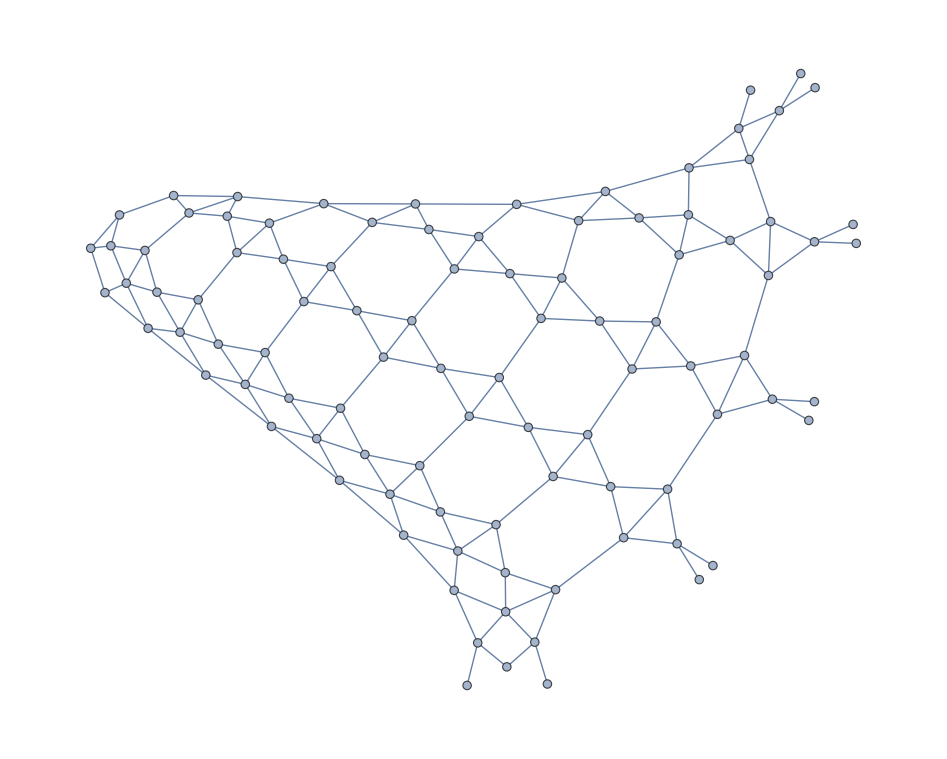

```mathematica
GraphPlot[#,VertexLabels->Placed[Automatic,Tooltip]]&@FromNetDifferenceSets@ExpandAll@
RollIC@RollIC@RollIC@RollIC@(
{IC[
IC[IC[{1,2},2],{3n,3n+1},n-1],{3n+2,3n+3},{1,2,3},{3n+3,3n+4},{1,2},{3n+1,3n+3},
IC[IC[{1,2},2],{3n+2,3n+3},n-1],{1,2},{1,3n+6},{3n+2,3n+3},{1,2,3},{3n+4,3n+5},{1,2},{3n+2,3n+4},
{n,1,4}]} /.IC->IndexedConcatenate)
```

```mathematica
/. IC->IndexedConcatenate//ExpandAll//FromNetDifferenceSets//GraphPlot[#,VertexLabels->Placed[Automatic,Tooltip]]&
```

```mathematica
RollIC@RollIC@RollIC@RollIC@(
{IC[
IC[IC[{1,2},2],{3n,3n+1},n-1],{3n+2,3n+3},{1,2,3},{3n+3,3n+4},{1,2},{3n+1,3n+3},
IC[IC[{1,2},2],{3n+2,3n+3},n-1],{1,2},{1,3n+6},{3n+2,3n+3},{1,2,3},{3n+4,3n+5},{1,2},{3n+2,3n+4},
{n,1,4}]} /.IC->IndexedConcatenate)
```

{€_(n⊨1)^4[{1,2,3},{3 n+1,3 n+2},{1,2},{3 n-1,3 n+1},€^(n-1)[€^2[{1,2}],{3 n,3 n+1}],{3 n+2,3 n+3},{1,2,3},{3 n+3,3 n+4},{1,2},{3 n+1,3 n+3},€^(n-1)[€^2[{1,2}],{3 n+2,3 n+3}],{1,2},{1,3 n+6},{3 n+2,3 n+3}]}

```mathematica
RollIC@RollIC@RollIC@RollIC@(
{IC[
IC[IC[{1,2},2],{3n,3n+1},n-1],{3n+2,3n+3},{1,2,3},{3n+3,3n+4},{1,2},{3n+1,3n+3},
IC[IC[{1,2},2],{3n+2,3n+3},n-1],{1,2},{1,3n+6},{3n+2,3n+3},{1,2,3},{3n+4,3n+5},{1,2},{3n+2,3n+4},
{n,1,4}]} /.IC->IndexedConcatenate)//InputForm
```

{IndexedConcatenate[{1, 2, 3}, {1 + 3*n, 2 + 3*n}, {1, 2}, {-1 + 3*n, 1 + 3*n}, IndexedConcatenate[IndexedConcatenate[{1, 2}, 2], {3*n, 1 + 3*n}, -1 + n], {2 + 3*n, 3 + 3*n}, {1, 2, 3}, {3 + 3*n, 4 + 3*n}, {1, 2}, 
  {1 + 3*n, 3 + 3*n}, IndexedConcatenate[IndexedConcatenate[{1, 2}, 2], {2 + 3*n, 3 + 3*n}, -1 + n], {1, 2}, {1, 6 + 3*n}, {2 + 3*n, 3 + 3*n}, {n, 1, 4}]}